# Chaotic Groundwater Mixing Near Tidally Forced Surface Water Bodies

Mike Trefry, May 2017
... updated 8 December 2017 with corrections for div-free Darcy flux at FD nodes, and enhanced SummaryPlot[]
... updated 4 January 2018 with explicit return of Continuity Equation residuals (steady and transient components), and corrected definition of Townley number
... updated 18 February 2018 with new LagrangianMeasures[] function to integrate 𝔽 directly, hence deprecating the FTLE[] function, which is now called FTLEdd[]
... updated 28 February 2018 to auto-detect underlying coordinate increment of log-k field and calculate ℓ_eff accordingly
... updated 1 March 2018 with Dan’s div-cleaning code for q_s and with matching of φ_p to ∇·q_p to honour the CE constraint
... updated 11 March 2018 with support for spatial averaging methods, explicit complex interpolation, and self-consistency check
... updated 26 March 2018 to behave more gracefully if J = (hL-h0)/L = 0, e.g. for Guy’s sub-problem. S=0 is explicitly not catered for
... updated 29 March 2018 to add PSectionRTDList[] that accepts a list of starting points for the Poincaré section (for Guy)
... updated 5 April 2018 to check tidal amplitude versus compressibility relation - detecting unphysical parameter combinations
... updated 8 April 2018 to add trajectory colouring ability in PSectionRTDList
... updated 1 May 2018 to store starting and ending points of extreme paths in RTD calculations; added version number support
... updated 9 May 2018 to define default Wolfram colours, to add the StitchSegment[] function, to add the PSectionRTDcc[] function for colour coding
...updated 21 May 2018 to enforce real-valued deformation gradient tensor in LagrangeMeasures[]
...updated 29 June 2018 to make parameters consistent with latest conventions, adding tidal compression ratio to the list as well
...updated 4 July 2018 to add flowmapX[] function (maxsteps->∞) and FTLEddP[] function to split the trajectory into sub-trajectories
...updated 5 July 2018 to correct typos in the FTLEddP[] function
...updated 25 July 2018 to correct LagrangeMeasures[] function, now calculates its own flowpath and exposes the 𝕃[t] and 𝔽[t] functions; also updated the dimensionless parameters to remove ℰ and put ℛ in instead
...updated 8 August 2018 to add the LagrangeMeasuresExplicit[] function, with explicit gradient function and improved NDSolve[] solution method; added FtoΛ[] function as well

This notebook supports the numerical analysis of chaotic groundwater flow zones near tidal boundaries. It employs the numerical finite-difference approach for solving a generalized hyperbolic dynamical equation (HDE, as described in Trefry et al., Phil. Trans. A, 368, 197-215, 2010) in the context of simple Darcian flow.

```mathematica
HDEVersion = "1.0.7";  (* to be incremented with every code change *)
```

## Core HDE Functions

```mathematica
Off[General::"spell1",InterpolatingFunction::"dmval",NDSolve::"impsitsf"];
NE[v_,p_:4]:=ScientificForm[v,p,NumberFormat->(Row[{#1,"E",#3}]&)]
ATanMGT[list_,unit_:1]:= ArcTan[list[[1]],list[[2]]]/unit
AffineNorm[list_]:= Abs[list[[1]]-list[[2]]]
MGTComplexListInterp2D[list_,domain_,opt:OptionsPattern[]]:= Module[{listR,listI,interpR,interpI,interpC},
listR = Re[list];
listI = Im[list];
interpR = ListInterpolation[listR,domain,opt];
interpI = ListInterpolation[listI,domain,opt];
interpC[x_,y_] = interpR[x,y] + ⅈ interpI[x,y];
Return[interpC[x,y]]
]
{WBlue,WOrange,WGreen,WRed,WPurple,WBrown,WAqua,WYellow} = Table[ColorData[97][i],{i,1,8}];
```

#### Conductivity field input

```mathematica
getK[filename_,data_,dx_]:= Module[{infile,databuffer,nx,ny,xmin,xmax,ymin,ymax},
infile = OpenRead[filename];
{nx,ny} = Read[infile,{Number,Number}];
{xmin,xmax} = Read[infile,{Real,Real}];
{ymin,ymax} = Read[infile,{Real,Real}];
databuffer = Partition[ReadList[infile,Number,nx*ny],ny];
data = Transpose[databuffer];
Close[infile];
dx = xmax/(nx-1);
]

getWindow[field_,ndim_,centroid_]:= Module[{nx,ny,ic=0,jc=0,wb},
{nx,ny} = Dimensions[field];
If[ndim>Min[nx-2,ny-2],Print["Input field smaller than requested window dimension "<>ToString[ndim]<>" - aborting!"]; Return[]];
If[StringQ[centroid]&&centroid == "random", ic = RandomInteger[{1+Ceiling[ndim/2],nx-Ceiling[ndim/2]}];jc = RandomInteger[{1+Ceiling[ndim/2],ny-Ceiling[ndim/2]}];];
If[VectorQ[centroid] && Length[centroid]≥2,{ic,jc} = {centroid[[1]],centroid[[2]]};];
If[ic==0 && jc==0,Print["Unrecognised centroid directive "<>ToString[centroid]<>" - aborting!"];Return[]];
If[!IntegerQ[ic] || !IntegerQ[jc],Print["Invalid centroid coordinates "<>ToString[{ic,jc}]<>" - aborting!"];Return[]];
If[ic<1+Ceiling[ndim/2] || ic>nx-Ceiling[ndim/2] || jc<1+Ceiling[ndim/2] || jc>ny-Ceiling[ndim/2],Print["Centroid coordinates "<>ToString[{ic,jc}]<>" too close to field edges - aborting!"]; Return[]];
Print["Extracting window of dimension "<>ToString[ndim]<>" from "<>ToString[{nx,ny}]<>" field centred at "<>ToString[{ic,jc}]<>"."];
wb = field[[ic-Ceiling[ndim/2];;ic-Ceiling[ndim/2]+ndim-1,jc-Ceiling[ndim/2];;jc-Ceiling[ndim/2]+ndim-1]];
Return[wb]
]
```

#### Spatial correlation functions

```mathematica
reorderFT1D[list_] := Module[{n=Length[list],Work1,Work2,ResultList},
If[Mod[n,2]==0,Work2 = Take[list,-n/2];,Work2 = Take[list,-(n-1)/2];];
If[Mod[n,2]==0,Work1 = Take[list,n/2];,Work1 = Take[list,1+(n-1)/2];];
ResultList = Join[Work2,Work1]
]
reorderFT2D[array_] := Module[{n=Length[array],Work1,Work2,tmpBuffer,ResultArray},
If[Mod[n,2]==0,Work1 = Take[array,All,-n/2];,Work1 = Take[array,All,-(n-1)/2];];
If[Mod[n,2]==0,Work2 = Take[array,All,n/2];,Work2 = Take[array,All,(n-1)/2];];
Do[ tmpBuffer = Work1[[kk]];
tmpBuffer = Join[tmpBuffer,Work2[[kk]]];
Work1[[kk]] = tmpBuffer;,{kk,1,Length[array]}];
ResultArray = Work1;
If[Mod[n,2]==0,Work1 = Take[ResultArray,n/2,All];,Work1 = Take[ResultArray,(n-1)/2,All];];
If[Mod[n,2]==0,Work2 = Take[ResultArray,-n/2,All];,Work2 = Take[ResultArray,-(n-1)/2,All];];
ResultArray = Join[Work2,Work1];
Return[ResultArray]
(*ResultArray/Max[Flatten[ResultArray]]*)
]
CrossCorrelation[list1_,list2_, normalized_]:= Module[{Work1},
If[Dimensions[list1] != Dimensions[list2],Print["list dimensions do not match";Abort[]]];
If[MatrixQ[list1], Work1 = reorderFT2D[ Chop[InverseFourier[Conjugate[Fourier[list1]] Fourier[list2]]]];,
Work1 = reorderFT1D[ Chop[InverseFourier[Conjugate[Fourier[list1]] Fourier[list2]]]];];
If[normalized == True,Work1/Max[Flatten[Work1]],Work1]
]
SpectralDensity[list1_] := Module[{Work1},
If[MatrixQ[list1], Work1 = reorderFT2D[ Chop[Conjugate[Fourier[list1]] Fourier[list1]]];,
Work1 = reorderFT1D[ Chop[Conjugate[Fourier[list1]] Fourier[list1]]];];
Return[Work1]
]
CrossSpectralDensity[list1_,list2_] := Module[{Work1},
If[Dimensions[list1] != Dimensions[list2],Print["list dimensions do not match";Abort[]]];
If[MatrixQ[list1], Work1 = reorderFT2D[ Chop[Fourier[list1]Conjugate[Fourier[list2]] ]];,
Work1 = reorderFT1D[ Chop[Fourier[list1]Conjugate[Fourier[list2]] ]];];
Return[Work1]
]
ensembleSD[field_,Nsamples_] := Module[{randomSamples,randomDirections,thisTrace,ensemble={},i},
randomSamples = RandomSample[Range[1,Min[Dimensions[field]]],Nsamples];
randomDirections = RandomInteger[Range[0,1],Nsamples];
Do[ If[randomDirections[[i]]==1,thisTrace = field[[randomSamples[[i]]]];,thisTrace = Transpose[field][[randomSamples[[i]]]];];
If[i==1,ensemble = SpectralDensity[thisTrace];,ensemble = ensemble+SpectralDensity[thisTrace];];,{i,1,Nsamples}];
Return[ensemble/(2 π Nsamples)]
]
kReference[list_,Nsamples_,scale_] := Module[{},
Table[{(i-Round[Nsamples/2])*(2π)/(Lx),scale*list[[i]]},{i,1,Nsamples}]
]
modulatedReference[list_,Nsamples_,scale_] := Module[{},
Table[{(i-Round[Nsamples/2])*(2π)/(Lx),scale*κGeom^2*((i-Round[Nsamples/2])*(2π)/(Lx))^2*list[[i]]/(λ^2 ω^2+κGeom^2((i-Round[Nsamples/2])*(2π)/(Lx))^4)},{i,1,Nsamples}]
]
```

#### Graphics functions

```mathematica
setRange[matrix_,rangemin_,rangemax_]:=Module[{tmpmatrix=matrix,dims=Dimensions[matrix]},tmpmatrix⟦1,1⟧=rangemax;tmpmatrix⟦dims⟦1⟧,dims⟦2⟧⟧=rangemin;Print[dims];tmpmatrix]
MGTRect[pos_,size_,filled_:True]:=If[filled==True,Rectangle[pos-size,pos+size],Line[{pos+{-1,-1} size,pos+{1,-1} size,pos+{1,1} size,pos+{-1,1} size,pos+{-1,-1} size}]]
MGTTriangle[pos_,size_,filled_:True]:=If[filled==True,Polygon[{pos+{-1,-Tan[π/6]} size,pos+{1,-Tan[π/6]} size,pos+{0,2 Sin[π/3]-Tan[π/6]} size,pos+{-1,-Tan[π/6]} size}],Polygon[{pos+{-1,-Tan[π/6]} size,pos+{1,-Tan[π/6]} size,pos+{0,2 Sin[π/3]-Tan[π/6]} size,pos+{-1,-Tan[π/6]} size}]]
getZ[list_,selection_]:=Module[{result={}},Do[If[Abs[list⟦i,1⟧-selection]<0.2,AppendTo[result,{list⟦i,2⟧,list⟦i,3⟧}]],{i,Length[list]}];result]
getH[list_]:=Module[{result={}},Do[AppendTo[result,{list⟦i,1⟧,list⟦i,4⟧}],{i,Length[list]}];result]
SummaryPlot[matrixRow_]:=Module[{minqqx,maxqqx,minqqy,maxqqy,FDgrid,qmean},
FDgrid = Table[{(i-1)*Δx,(j-1)*Δy},{i,1,nx},{j,1,ny}];
qmean = If[J==0,1,(-κeff(hL-h0)/L)];
qqx = Transpose[Table[Log[Chop[qDsx[i,j]]/qmean],{i,1,nx},{j,1,ny}]];
qqy = Transpose[Table[Chop[qDsy[i,j]]/(-qmean),{i,1,nx},{j,1,ny}]];
{minqqx,maxqqx} = {Min[Re[Flatten[qqx]]],Max[Re[Flatten[qqx]]]};
{minqqy,maxqqy} = {Min[Re[Flatten[qqy]]],Max[Re[Flatten[qqy]]]};
Show[GraphicsGrid[{{ListDensityPlot[Transpose[Log[κarray]],AspectRatio->Automatic,Mesh->False,Axes->False,Frame->False,PlotRange->All,ColorFunction->"CoffeeTones",Epilog->{RGBColor[0,1,0],Line[{{1,matrixRow},{Length[uProfile[matrixRow]],matrixRow}}]},PlotRegion->{{0,1},{0,1}},PlotLabel->"Log κ",ImageSize->{280,280},BaseStyle->{16,FontFamily->"Times"},DisplayFunction->Identity],Histogram[Log[Flatten[κarray]]-logκMean,{-(Ceiling[3*logκVariance]+1),Ceiling[3*logκVariance]+1,0.2},"Probability",Frame->True,AspectRatio->1,PlotRegion->{{0.05,0.95},{0.05,0.95}},PlotLabel->"κ Distribution",FrameLabel->{Style["log κ/κ_eff",20,FontFamily->Times],Style["probability",FontFamily->Times,20],"",""},LabelStyle->Black,ChartStyle->{RGBColor[0.8,0.8,0.8]},Epilog->{Thickness[0.02],Line[{{Log[logκMean/logκMean],0},{Log[logκMean/logκMean],0.10}}]},DisplayFunction->Identity,BaseStyle->{16,FontFamily->"Times"}]},
{Overlay[{ListDensityPlot[Transpose[Log[κarray]],ColorFunction->"CoffeeTones",AspectRatio->Automatic,Mesh->False,Axes->False,Frame->False,ImageSize->{280,280},PlotLabel->"Steady Flux Lines",BaseStyle->{16,FontFamily->"Times"},Epilog->{RGBColor[0,1,0],Line[{{0,matrixRow},{Length[uProfile[matrixRow]],matrixRow}}]},DisplayFunction->Identity],ListStreamPlot[Table[{{(i-1.)*Δx,(j-1.)*Δy},qDs[i,j]//Chop},{i,1,nx},{j,1,ny}],Frame->False,StreamStyle->Black,PlotLabel->" ",BaseStyle->{16,FontFamily->"Times"},PlotRange->{{0,L},{0,L}},StreamPoints->Fine,VectorPoints->0,VectorStyle->Red,ImageSize->{280,280},DisplayFunction->Identity]},ContentPadding->True],
Plot[hL x,{x,0,1},PlotRange->{{-0.0001,1},{-0.0001,1.00001}},PlotStyle->{RGBColor[0,0,0],Black},Frame->True,AspectRatio->1,FrameTicks->{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,0.1},{},{0,0.2,0.4,0.6,0.8,{0.999999,1}}},FrameLabel->{Style["x",20,Italic],Style["u_s",20,Italic],"",""},LabelStyle->Black,PlotLabel->"Steady Head Section",Epilog->{PointSize[0.015],(MGTRect[#1,{0.01,0.01}]&)/@Table[{hProfile[matrixRow]⟦i,1⟧,Abs[hProfile[matrixRow]⟦i,2⟧]},{i,Length[hProfile[matrixRow]]}]},BaseStyle->{16,FontFamily->"Times"}]},
{ListDensityPlot[qqx,PlotRange->All,Frame->False,PlotLabel->"Log(q_x/q̄)",DataRange->{{0,1},{0,1}},BaseStyle->{16,FontFamily->"Times"},Epilog->{PointSize[0.01],Point/@FDgrid},PlotLegends->Automatic,ColorFunction->(Blend[{{minqqx,Blue},{0,White},{maxqqx,Orange}},#]&),ColorFunctionScaling->False],
ListDensityPlot[qqy,PlotRange->All,Frame->False, PlotLabel->"q_y/|q̄|",DataRange->{{0,1},{0,1}},BaseStyle->{16,FontFamily->"Times"},Epilog->{PointSize[0.01],Point/@FDgrid},PlotLegends->Automatic,ColorFunction->(Blend[{{minqqy,Blue},{0,White},{maxqqy,Orange}},#]&),ColorFunctionScaling->False]},
{ListDensityPlot[Transpose[Abs[Partition[u,ny]]],AspectRatio->Automatic,Mesh->False,Axes->False,Frame->False,ColorFunctionScaling->False,PlotRange->{0,1},PlotRegion->{{0,1},{0,1}},PlotLabel->"Oscillation Amplitude",Epilog->{RGBColor[0,1,0],Line[{{1,matrixRow},{Length[uProfile[matrixRow]],matrixRow}}]},BaseStyle->{16,FontFamily->"Times"},DisplayFunction->Identity],ListDensityPlot[Φ[Transpose[MArg[Chop[Partition[u,ny]]]]],AspectRatio->Automatic,Mesh->False,Axes->False,ColorFunctionScaling->False,Frame->False,PlotRange->{0,1},  PlotLabel->"Oscillation Phase",BaseStyle->{16,FontFamily->"Times"},
PlotRegion->{{0,1},{0,1}},Epilog->{RGBColor[0,1,0],Line[{{1,matrixRow},{Length[uProfile[matrixRow]],matrixRow}}]},DisplayFunction->Identity]},
{Plot[{Abs[uHyperbolicConstantDN[x,L,ω,κGeom,λ,τ,1,0]],Φ[Arg[uHyperbolicConstantDN[x,L,ω,κGeom,λ,τ,1,0]]]},{x,0,1},PlotRange->{{-0.0001,1},{-0.0001,1.00001}},PlotStyle->{RGBColor[0,0,0],{RGBColor[0,0,0],Dashing[{0.02,0.01}]}},Frame->True,AspectRatio->1,Axes->True,LabelStyle->Black,PlotLabel->"Oscillation Functions in Section",FrameTicks->{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,0.1},{},{0,0.2,0.4,0.6,0.8,{0.999999,1}}},FrameLabel->{Style["x",20,Italic],Row[{Style["|",FontFamily->Times,20],Style["u_p",FontFamily->Times,20,Italic],Style["|",20,FontFamily->Times],Style[" and Φ(arg u_p)",FontFamily->Times,20]}],"",""},Epilog->{PointSize[0.015],(MGTRect[#1,{0.01,0.01}]&)/@Table[{uProfile[matrixRow]⟦i,1⟧,Abs[uProfile[matrixRow]⟦i,2⟧]},{i,Length[uProfile[matrixRow]]}],(Circle[#1,0.008]&)/@Table[{uProfile[matrixRow]⟦i,1⟧,Φ[MArg[uProfile[matrixRow]⟦i,2⟧]]},{i,Length[uProfile[matrixRow]]}]},DisplayFunction->Identity,BaseStyle->{16,FontFamily->"Times"}],ParametricPlot[{Log[Abs[uHyperbolicConstantDN[x,L,ω,κGeom,λ,τ,1,0]]],Φ[Arg[uHyperbolicConstantDN[x,L,ω,κGeom,λ,τ,1,0]]]},{x,0,1},Frame->True,PlotRange->{{-6,0},{0,1}},PlotRegion->{{0.05,0.95},{0.05,0.95}},AspectRatio->1,PlotStyle->{Black},LabelStyle->Black,PlotLabel->"Propagation Curve",FrameLabel->{Row[{Style["Log |",FontFamily->Times,20],Style["u_p",FontFamily->Times,20,Italic],Style["|",FontFamily->Times,20]}],"","",Row[{Style["Φ(arg ",FontFamily->Times,20],Style["u_p",FontFamily->Times,20,Italic],Style[")",FontFamily->Times,20]}]},FrameTicks->{{{-5.99999,-6},-5,-4,-3,-2,-1,0},{},{},{0,0.2,0.4,0.6,0.8,{0.999999,1}}},Epilog->{PointSize[0.015],(Circle[#1,{0.032,0.008}]&)/@Table[{Log[Abs[uProfile[matrixRow]⟦i,2⟧]],Φ[MArg[uProfile[matrixRow]⟦i,2⟧]]},{i,Length[uProfile[matrixRow]]}]},DisplayFunction->Identity,BaseStyle->{16,FontFamily->"Times"}]}},
DisplayFunction->$DisplayFunction]]
]

makeScale[]:=ListDensityPlot[Table[(j-1) 0.01,{i,1,8},{j,1,101}],AspectRatio->Automatic,Frame->True,Axes->False,Mesh->False,ColorFunction->(RGBColor[#,#,#]&)]
```

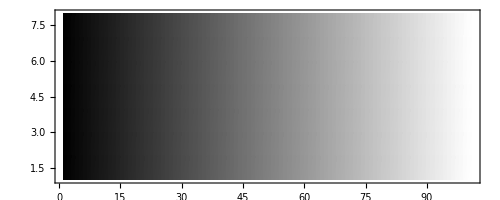

```mathematica
makeScale[]
```

#### Exact periodic solution

```mathematica
uHyperbolicConstantDN[x_,Λ_,ω_,κ0_,λ0_,τ0_,ϕ0_,ϕ1_] :=1/γ[ω,κ0,λ0,τ0](Sech[γ[ω,κ0,λ0,τ0] Λ] (γ[ω,κ0,λ0,τ0] ϕ0 Cosh[γ[ω,κ0,λ0,τ0] (x-Λ)]+ϕ1 Sinh[x γ[ω,κ0,λ0,τ0]]))
γ[ω_,κ0_,λ0_,τ0_] := (√(λ0 ω (ⅈ-τ0 ω)))/(√κ0)
```

```mathematica
uHyperbolicConstantDN[x,LL,ωω,κκ,λλ,τ,1,0]
```

Cosh[((-LL+x) √(λλ ωω (ⅈ-τ ωω)))/(√κκ)] Sech[(LL √(λλ ωω (ⅈ-τ ωω)))/(√κκ)]

#### Discretized solution of the HDE

```mathematica
Φ[Δϕ_]:=Piecewise[{{-Δϕ/(2 π), Δϕ≤0}, {1-Δϕ/(2 π), Δϕ>0}}]
SetAttributes[Φ,Listable];
MArg[z_]:=Which[z == 0,0,True,Arg[z]]
SetAttributes[MArg,Listable];
κfuncA[x_,y_]:= Module[{i,j,imin,imax,jmin,jmax,κestimate},
If[Δx*Floor[x/Δx] == x,i=x/Δx+1;imin=i;imax=i;,imin=Floor[x/Δx]+1;imax=Ceiling[x/Δx]+1;];
If[Δy*Floor[y/Δy] == y,j=y/Δy+1;jmin=j;jmax=j;,jmin=Floor[y/Δy]+1;jmax=Ceiling[y/Δy]+1;];
Which[ imin == imax, κestimate = (κarray[[imin,jmin]]+κarray[[imin,jmax]])/2;,jmin==jmax, κestimate=(κarray[[imin,jmin]]+κarray[[imax,jmin]])/2;];
κestimate
]
κfuncH[x_,y_]:= Module[{i,j,imin,imax,jmin,jmax,κestimate},
If[Δx*Floor[x/Δx] == x,i=x/Δx+1;imin=i;imax=i;,imin=Floor[x/Δx]+1;imax=Ceiling[x/Δx]+1;];
If[Δy*Floor[y/Δy] == y,j=y/Δy+1;jmin=j;jmax=j;,jmin=Floor[y/Δy]+1;jmax=Ceiling[y/Δy]+1;];
Which[ imin == imax, κestimate = 2(1/κarray[[imin,jmin]]+1/κarray[[imin,jmax]])^-1;,jmin==jmax, κestimate=2(1/κarray[[imin,jmin]]+1/κarray[[imax,jmin]])^-1;];
κestimate
]
κfuncG[x_,y_]:= Module[{i,j,imin,imax,jmin,jmax,κestimate},
If[Δx*Floor[x/Δx] == x,i=x/Δx+1;imin=i;imax=i;,imin=Floor[x/Δx]+1;imax=Ceiling[x/Δx]+1;];
If[Δy*Floor[y/Δy] == y,j=y/Δy+1;jmin=j;jmax=j;,jmin=Floor[y/Δy]+1;jmax=Ceiling[y/Δy]+1;];
Which[ imin == imax, κestimate =√(κarray[[imin,jmin]]κarray[[imin,jmax]]) ;,jmin==jmax, κestimate=√(κarray[[imin,jmin]]κarray[[imax,jmin]]);];
κestimate
]
κfuncFD[x_,y_] := Switch[FDAveragingMethod,"arithmetic",κfuncA[x,y],"harmonic",κfuncH[x,y],"geometric",κfuncG[x,y],_,Print["bad value for FDAveragingMethod: ",FDAveragingMethod];0]
τfuncH[x_,y_]:= τarray[[x/Δx+1,y/Δy+1]]
ϵfuncH[x_,y_]:= ϵarray[[x/Δx+1,y/Δy+1]]
M2DinteriorDiscrete[i_,j_,ω_] := Module[{k},
k = (i-1)*ny + j ; 
LE2DM[[k,k]] = -(κfuncFD[(i-1/2)*Δx,(j-1)*Δy]+κfuncFD[(i-3/2)*Δx,(j-1)*Δy])/Δx^2-(κfuncFD[(i-1)*Δx,(j-1/2)*Δy]+κfuncFD[(i-1)*Δx,(j-3/2)*Δy])/Δy^2 +
ω*λ(-1-  ⅈ *ω* τfuncH[(i-1)*Δx,(j-1)*Δy])/(-ⅈ+ ω*ϵfuncH[(i-1)*Δx,(j-1)*Δy]+ ω*λ*β^2);
LE2DM[[k,k-ny]] =  κfuncFD[(i-3/2)*Δx,(j-1)*Δy]/Δx^2+(ω*κfuncFD[(i-1)*Δx,(j-1)*Δy](τfuncH[(i-2)*Δx,(j-1)*Δy]-τfuncH[i*Δx,(j-1)*Δy]))/(4 Δx^2(ⅈ-ω*τfuncH[(i-1)*Δx,(j-1)*Δy]))+ (ⅈ*ω*κfuncH[(i-1)*Δx,(j-1)*Δy] (ϵfuncH[(i-2)*Δx,(j-1)*Δy]-ϵfuncH[i*Δx,(j-1)*Δy]))/(4 Δx^2 (1+ⅈ *ω *ϵfuncH[(i-1)*Δx,(j-1)*Δy]+ ⅈ *ω *λ *β^2));
LE2DM[[k,k+ny]] = κfuncFD[(i-1/2)*Δx,(j-1)*Δy]/Δx^2+(ω*κfuncFD[(i-1)*Δx,(j-1)*Δy](-τfuncH[(i-2)*Δx,(j-1)*Δy]+τfuncH[i*Δx,(j-1)*Δy]))/(4 Δx^2(ⅈ-ω*τfuncH[(i-1)*Δx,(j-1)*Δy]))+ (ⅈ*ω*κfuncFD[(i-1)*Δx,(j-1)*Δy] (-ϵfuncH[(i-2)*Δx,(j-1)*Δy]+ϵfuncH[i*Δx,(j-1)*Δy]))/(4 Δx^2 (1+ⅈ *ω *ϵfuncH[(i-1)*Δx,(j-1)*Δy]+ ⅈ *ω* λ* β^2));
LE2DM[[k,k-1]] = κfuncFD[(i-1)*Δx,(j-3/2)*Δy]/Δy^2+(ω*κfuncFD[(i-1)*Δx,(j-1)*Δy](τfuncH[(i-1)*Δx,(j-2)*Δy]-τfuncH[(i-1)*Δx,j*Δy]))/(4 Δy^2(ⅈ-ω*τfuncH[(i-1)*Δx,(j-1)*Δy]))+(ⅈ*ω*κfuncFD[(i-1)*Δx,(j-1)*Δy](ϵfuncH[(i-1)*Δx,(j-2)*Δy]-ϵfuncH[(i-1)*Δx,j*Δy]))/(4 Δx^2 (1+ⅈ *ω *ϵfuncH[(i-1)*Δx,(j-1)*Δy]+ ⅈ *ω* λ* β^2));
LE2DM[[k,k+1]] = κfuncFD[(i-1)*Δx,(j-1/2)*Δy]/Δy^2+(ω*κfuncFD[(i-1)*Δx,(j-1)*Δy](-τfuncH[(i-1)*Δx,(j-2)*Δy]+τfuncH[(i-1)*Δx,j*Δy]))/(4 Δy^2(ⅈ-ω*τfuncH[(i-1)*Δx,(j-1)*Δy]))+(ⅈ*ω*κfuncFD[(i-1)*Δx,(j-1)*Δy](-ϵfuncH[(i-1)*Δx,(j-2)*Δy]+ϵfuncH[(i-1)*Δx,j*Δy]))/(4 Δx^2 (1+ⅈ *ω *ϵfuncH[(i-1)*Δx,(j-1)*Δy]+ ⅈ *ω* λ* β^2));
]
DirichletConditionM2D[boundary_,k_,value_]:=Module[{},Which[boundary=="left" || boundary== "top", LE2DM[[k,k]] = 1; LE2DB[[k]] = value;,
boundary=="right" || boundary=="bottom",LE2DM[[k,k]] = 1;  LE2DB[[k]] = value;];]
NeumannConditionM2D[boundary_,k_,value_]:=Module[{},Which[boundary=="left" ,LE2DM[[k,k]] = -1/Δx; LE2DM[[k,k+ny]] = 1/Δx; LE2DB[[k]] =value;,
boundary== "top",LE2DM[[k,k]] = -1/Δy; LE2DM[[k,k+1]] = 1/Δy; LE2DB[[k]] =value;,
boundary=="right", LE2DM[[k,k-ny]] = -1/Δx;LE2DM[[k,k]] = 1/Δx; LE2DB[[k]] =value;,
boundary=="bottom", LE2DM[[k,k-1]] = -1/Δy;LE2DM[[k,k]] = 1/Δy; LE2DB[[k]] =value;];]
CauchyConditionM2D[boundary_,k_,coeff1_,coeff2_,value_] :=Module[{},Which[boundary=="left" ,LE2DM[[k,k]] = coeff1-coeff2/Δx; LE2DM[[k,k+ny]] = coeff2/Δx; LE2DB[[k]] =value;,
boundary=="top" ,LE2DM[[k,k]] = coeff1-coeff2/Δy; LE2DM[[k,k+1]] = coeff2/Δy; LE2DB[[k]] =value;,
boundary=="right", LE2DM[[k,k-ny]] = -coeff2/Δx;LE2DM[[k,k]] = coeff1+coeff2/Δx; LE2DB[[k]] =value;,
boundary=="bottom", LE2DM[[k,k-1]] = -coeff2/Δy;LE2DM[[k,k]] = coeff1+coeff2/Δy; LE2DB[[k]] =value;];]
M2DboundarySteady[i_,j_,h0_,h1_] := Module[{},
k = (i-1)*ny + j ;
Which[ k <= ny, DirichletConditionM2D["left",k,h0];,
k > (nx-1)*ny, DirichletConditionM2D["right",k,h1];,
j == 1, NeumannConditionM2D["top",k,0];,
j == ny,  NeumannConditionM2D["bottom",k,0];];
]
M2DboundaryPeriodic[i_,j_,u0_] := Module[{},
k = (i-1)*ny + j ;
Which[ k <= ny, DirichletConditionM2D["left",k,u0];,
k > (nx-1)*ny, NeumannConditionM2D["right",k,0];,
j == 1, NeumannConditionM2D["top",k,0];,
j == ny,  NeumannConditionM2D["bottom",k,0];];
]
M2DstencilDiscreteSteady[p_,q_,h0_,h1_] := If[ p>1 && p < nx && q > 1 && q < ny, M2DinteriorDiscrete[p,q,0],M2DboundarySteady[p,q,h0,h1]]
M2DstencilDiscretePeriodic[p_,q_,u0_,ω_] := If[ p>1 && p < nx && q > 1 && q < ny, M2DinteriorDiscrete[p,q,ω],M2DboundaryPeriodic[p,q,u0]]

(* SolutionFlux calculates Darcian flux vector with linear interpolation of conductivities and simple
differencing for head gradients *)
SolutionFluxOld[Ψ_,K_,Lx_,Ly_]:= Module[{fnx,fny,dx,dy,flux={},cond,i,j},
{fny,fnx}=Dimensions[Ψ];
{dx,dy} = {Lx/(nx-1),Ly/(ny-1)};
flux = Table[{0,0},{j,1,fny},{i,1,fnx}];
cond = ListInterpolation[K,InterpolationOrder->{1,1}];
Do[ flux[[j,i]] = -{(cond[j,i](Ψ[[j,i+1]]-Ψ[[j,i-1]]))/(2 dx),(cond[j,i](Ψ[[j+1,i]]-Ψ[[j-1,i]]))/(2 dy)},{i,2,fnx-1},{j,2,fny-1}];
Do[ flux[[j,1]] = -{(cond[j,3/2](Ψ[[j,2]]-Ψ[[j,1]]))/dx,(cond[j,1](Ψ[[j+1,1]]-Ψ[[j-1,1]]))/(2 dy)};
flux[[j,fnx]] =- {1/dx cond[j,fnx-1/2](Ψ[[j,fnx]]-Ψ[[j,fnx-1]]),1/(2 dy)cond[j,fnx](Ψ[[j+1,fnx]]-Ψ[[j-1,fnx]])},{j,2,fny-1}];
Do[ flux[[1,i]] = -{(cond[1,i](Ψ[[1,i+1]]-Ψ[[1,i-1]]))/(2 dx),(cond[3/2,i](Ψ[[2,i]]-Ψ[[1,i]]))/dy};
flux[[fny,i]] = -{1/(2 dx)cond[fny,i](Ψ[[fny,i+1]]-Ψ[[fny,i-1]]),1/dy cond[fny,i](Ψ[[fny,i]]-Ψ[[fny-1,i]])},{i,2,fnx-1}];
flux[[1,1]] = (flux[[2,1]]+flux[[1,2]])/2;
flux[[1,nx]] = (flux[[1,nx-1]]+flux[[2,nx]])/2;
flux[[ny,1]] = (flux[[ny,2]]+flux[[ny-1,1]])/2;
flux[[ny,nx]] = (flux[[ny,nx-1]]+flux[[ny-1,nx]])/2;
flux 
]

(* KH calculates the arithmetic average of two entries in the two-dimensional K list *)
KA[K_,i1_,j1_,i2_,j2_]:=(K[[i1,j1]]+K[[i2,j2]])/2

(* KH calculates the harmonic average of two entries in the two-dimensional K list *)
KH[K_,i1_,j1_,i2_,j2_]:=(2 K[[i1,j1]]K[[i2,j2]])/(K[[i1,j1]]+K[[i2,j2]])

(* KH calculates the geometric average of two entries in the two-dimensional K list *)
KG[K_,i1_,j1_,i2_,j2_]:= √(K[[i1,j1]]K[[i2,j2]])

KFD[K_,i1_,j1_,i2_,j2_]:= Switch[FDAveragingMethod,"arithmetic",KA[K,i1,j1,i2,j2],"harmonic",KH[K,i1,j1,i2,j2],"geometric",KG[K,i1,j1,i2,j2],_,Print["bad value for FDAveragingMethod: ",FDAveragingMethod];0]

(* SolutionFlux calculates the div-free Darcian flux vector (single-sided) on the finite-difference grid with harmonic averaging of conductivities *)
SolutionFlux[Ψ_,K_,Lx_,Ly_]:= Module[{fnx,fny,dx,dy,flux={},i,j,ceD,ce},
{fny,fnx}=Dimensions[Ψ];
{dx,dy} = {Lx/(nx-1),Ly/(ny-1)};
qDsx[i_,j_]:= Which[i==fnx,-KFD[K,i,j,i-1,j](Ψ[[i,j]]-Ψ[[i-1,j]])/dx,
i==0,-KFD[K,2,j,1,j](Ψ[[2,j]]-Ψ[[1,j]])/dx,
True,-KFD[K,i,j,i+1,j](Ψ[[i+1,j]]-Ψ[[i,j]])/dx];
qDsy[i_,j_]:= Which[j==fny,-KFD[K,i,j,i,j-1](Ψ[[i,j]]-Ψ[[i,j-1]])/dy,
j==0,-KFD[K,i,2,i,1](Ψ[[i,2]]-Ψ[[i,1]])/dy,
True,-KFD[K,i,j,i,j+1](Ψ[[i,j+1]]-Ψ[[i,j]])/dy];
qDs[i_,j_]:= {qDsx[i,j],qDsy[i,j]};
flux = Table[qDs[i,j],{i,1,fnx},{j,1,fny}];
ceD[i_,j_]:=Which[i≥2 && j≥2,(qDsx[i,j]-qDsx[i-1,j])/dx + (qDsy[i,j]-qDsy[i,j-1])/dy,
i==1 && j ≥2,(qDsy[i,j]-qDsy[i,j-1])/dy,
i≥2 && j==1, (qDsx[i,j]-qDsx[i-1,j])/dx ,
i==1 && j==1,0];
ce = Table[ceD[i,j],{i,1,fnx},{j,1,fny}];
Return[{flux,ce}]
]

(* DiscretePathline calculates a pathline through the steady flux field, using linear interpolation 
of flux components and a simple Eulerian temporal integration *)
DiscretePathline[v_List,Lx_,Ly_,p0_List,tmax_,sense_] := Module[{nx,ny,dx,dy,ndim,dt,px,py,pxold,pyold,t,maxvelc,vel,cond,counter,maxcounter=1000},
{nx,ny,ndim} = Dimensions[v];
{dx,dy}={Lx/(nx-1),Ly/(ny-1)};
vel = ListInterpolation[v,{{0,Ly},{0,Lx},{1,2}},InterpolationOrder->{1,1,1}];
maxvelc = Max[Flatten[Abs[v]]];
dt = 0.5*Sign[sense]*Min[dx,dy]/maxvelc;
Print["dt = ",N[dt]," with maximum velocity component = ",N[maxvelc]];
t=0;path = {{t,p0[[1]],p0[[2]]}};counter=0;{px,py}=p0;{pxold,pyold}=p0;
While[(0<=px<=Lx) && (0<=py<=Ly) && (Abs[t]<=tmax) && (counter<=maxcounter),
px += dt*vel[pyold,pxold,1];
py += dt*vel[pyold,pxold,2];
t += dt;
counter +=1;
path = Append[path,{t,px,py}];
pxold = px;
pyold = py;
];
path = Drop[path,-1]
]

(* TimePath splits a list of {t,x,y} coordinates into a series of consecutive line segments
each preceded by a RGBColor directive displaying the fraction of total path time *)
TimePath[list_List]:= Module[{result={},thisDuration,thisTimeFraction},
thisDuration =Abs[ list[[-1,1]]]-Abs[list[[1,1]]];
Do[thisTimeFraction = list[[i,1]]/thisDuration;
result = Append[result,{RGBColor[thisTimeFraction,0,1-thisTimeFraction],Line[{{list[[i-1,2]],list[[i-1,3]]},{list[[i,2]],list[[i,3]]}}]}];,{i,2,Length[list]}];
result
]

(* SpeedPath splits a list of {t,x,y} coordinates into a series of consecutive line segments
each preceded by a RGBColor directive displaying the fraction of maximum speed along the path *)
SpeedPath[list_List,usearrows_,shadepaths_,flatcolour_]:= Module[{result={},thisSpeed={},thisMaxSpeed,thisSpeedFraction,arrowcounter=0,shades,cf},
shades=Join[{"Black","Blue","Brown","Cyan","Gray","Green","Magenta","Orange","Pink","Purple","Red","White","Yellow"},AllColors];
If[shadepaths==False && Select[shades,# ===flatcolour &]=={},Print["Colour ",flatcolour," not supported - changing to White"];cf=RGBColor[1,1,1];,cf =ToExpression[flatcolour];];
If[shadepaths==True,cf = RGBColor[thisSpeedFraction^2,0,√(1-thisSpeedFraction)];];
thisSpeed = {};
Do[ thisSpeed = Append[thisSpeed, (√((list[[i,2]]-list[[i-1,2]])^2+(list[[i,3]]-list[[i-1,3]])^2))/(list[[i,1]]-list[[i-1,1]])],{i,2,Length[list]}];
thisMaxSpeed =Max[ thisSpeed];
Do[thisSpeedFraction = (√((list[[i,2]]-list[[i-1,2]])^2+(list[[i,3]]-list[[i-1,3]])^2))/(list[[i,1]]-list[[i-1,1]])/thisMaxSpeed;
arrowcounter++;
If[usearrows == True &&Mod[ arrowcounter,100]==10,result = Append[result,{cf,Arrow[{list[[i-1,2]],list[[i-1,3]]},{list[[i,2]],list[[i,3]]},HeadScaling->Absolute],Line[{{list[[i-1,2]],list[[i-1,3]]},{list[[i,2]],list[[i,3]]}}]}];,
result = Append[result,{cf,Line[{{list[[i-1,2]],list[[i-1,3]]},{list[[i,2]],list[[i,3]]}}]}];];,{i,2,Length[list]}];
result
]

(* PorosityComponents calculates the steady and periodic components for the first-order compressible porosity φ using the steady and periodic head solutions *)
PorosityComponents[hs_,hp_,storativity_,href_,φref_]:= Module[{nx,ny,φs={},φp={},i,j},
{ny,nx}=Dimensions[hs];
φs = Table[0,{j,1,ny},{i,1,nx}];
φp = Table[0,{j,1,ny},{i,1,nx}];
Do[ φs[[j,i]]= φref + storativity*(hs[[j,i]]-href);
φp[[j,i]]=  storativity*hp[[j,i]],{i,1,nx},{j,1,ny}];
{φs,φp}
]
```

#### Divergence Cleaner and Continuity Equation Test

Code written by Dan Lester to construct a streamfunction ψ from input continuous v_x[x,y] and v_y[x,y] functions (via integration) and then establish divergence-free counterparts w_x and w_y.

```mathematica
DivClean[vx_,vy_,knots_]:= Module[{xmin,xmax,ymin,ymax,Nknots=knots,Nxknots,Nyknots,hx,hy,ψdat,ψXdat,ψYdat,ψ,soln,j,k,wx,wy,δ=0.02,meanvx,relerr},
xmin=0;xmax=1;
ymin=0;ymax=1;
Nxknots=Nknots;
Nyknots=Nknots;
hx=(xmax-xmin)/(Nxknots-1);
hy=(ymax-ymin)/(Nyknots-1);
ψXdat=Table[0,{Nxknots},{Nyknots}];
ψYdat=Table[0,{Nxknots},{Nyknots}];
Do[
soln[y_]=NDSolve[{Ψ'[y]==vx[xmin+j hx,y],Ψ[ymin]==0},Ψ[y],{y,ymin,ymax},AccuracyGoal->12,PrecisionGoal->12][[1,1,2]];
ψXdat[[j]]=Table[soln[ymin+k hy],{k,Nyknots}],{j,Nxknots}];
Do[
soln[x_]=NDSolve[{Ψ'[x]==-vy[x,ymin+j hy],Ψ[xmin]==0},Ψ[x],{x,xmin,xmax},AccuracyGoal->12,PrecisionGoal->12][[1,1,2]];
ψYdat[[j]]=Table[soln[xmin+k hx],{k,Nxknots}],{j,Nyknots}];
ψdat=((ψXdat+ψYdat[[1]])ᵀ+ψYdat+ψXdat[[1]])/2;
ψ[x_,y_]=ListInterpolation[ψdatᵀ,{{xmin,xmax},{ymin,ymax}}][x,y];
wx[x_,y_]=D[ψ[x,y], y];
wy[x_,y_]=-D[ψ[x,y], x];
meanvx=Norm[Flatten[Table[wx[x,y],{x,xmin,xmax,δ},{y,ymin,ymax,δ}]]];
relerr = Norm[Flatten[Table[(wx[x,y]-vx[x,y]),{x,xmin,xmax,δ},{y,ymin,ymax,δ}]]]/meanvx;
Return[{wx,wy,ψ,relerr}];
]
```

Simple tests for our flux and porosity solutions

```mathematica
SteadyDivergence[qx_,qy_]:=If[J==0,0,Div[{qx,qy},{x,y}]]
ContinuityEquation[qx_,qy_,φ_]:= Div[{qx,qy},{x,y}] + D[φ, t]//FullSimplify
```

#### Solution utility functions

```mathematica
uProfile[i_]:=If[1≤i≤nx,Table[{(k-1) Δx,Transpose[Partition[u,ny]]⟦i⟧⟦k⟧},{k,1,nx}],Print["index out of bounds"];]
hProfile[i_]:=If[1≤i≤nx,Table[{(k-1) Δx,Transpose[Partition[h,ny]]⟦i⟧⟦k⟧},{k,1,nx}],Print["index out of bounds"];]
uProfileCross[i_]:=If[1≤i≤ny,Table[{(k-1) Δy,Partition[u,ny]⟦i⟧⟦k⟧},{k,1,ny}]]
GreenGhost[val_]:=RGBColor[val,val^0.5,val/2]
FireBird[val_]:=RGBColor[val^0.24,val^0.5,1-val^3]
graphAbsProfile[k_]:=ListPlot[Abs[uProfile[k]],Joined->True,PlotRange->{{-0.00001,L},{-0.00001,1}},Frame->True,Epilog->{PointSize[0.02],Point/@Abs[uProfile[k]]}]
graphArgProfile[k_]:=ListPlot[Table[{uProfile[k]⟦i,1⟧,Φ[MArg[uProfile[k]⟦i,2⟧]]},{i,Length[uProfile[k]]}],Joined->True,PlotRange->{{-0.00001,L},{-0.00001,1}},Frame->True,Epilog->{PointSize[0.02],Point/@Table[{uProfile[k]⟦i,1⟧,Φ[MArg[uProfile[k]⟦i,2⟧]]},{i,Length[uProfile[k]]}]}]
```

#### Dynamical utility functions

```mathematica
ConvexPolygonArea[vertices_]:=(1/2)*(Sum[Det[Transpose[{vertices[[i]],vertices[[i+1]]}]],{i,1,Length[vertices]-1}] + Det[Transpose[{vertices[[-1]],vertices[[1]]}]])
PolygonSense[convexarea_] := Which[convexarea<0,"clockwise",convexarea==0,0,convexarea>0,"anticlockwise"]
analyzeEllipse[xc_,yc_,ξ_,ψ_,μ_,ν_] := 
Module[{pe,pepoints,nsamples=50,pemean,newpts,uu,vv,ww,persqr,newx,newy,peexpr,peregion,pesense,pea,peb,peφ,pecp,peecc,pecanonical},
pe[t_]:= {xc+ξ Cos[t]-ψ Sin[t],yc+μ Cos[t] - ν Sin[t]};
pepoints = Table[pe[t],{t,0,2π,2.π/nsamples}];
pemean = {xc,yc};
newpts=Map[#-pemean&,pepoints];
{uu,ww,vv}=SingularValueDecomposition[newpts,2];
persqr=Mean[Map[#.#&,uu]];
{newx,newy}=Inverse[vv.ww].({x,y}-pemean);
peexpr=Expand[newx^2+newy^2]==persqr;
peregion=Expand[newx^2+newy^2]<=persqr;
pesense = ConvexPolygonArea[pepoints]//PolygonSense;
pea =Abs[ (ξ √(ν^2+ψ^2))/ν]; peb = √(ν^2+ψ^2); peφ = ArcTan[-ν/(√(ν^2+ψ^2)),ψ/(√(ν^2+ψ^2))];
peecc = Which[pea>peb,pea/peb,pea<peb,peb/pea,pea==peb,1];

pecanonical = Which[peregion/.{x->0,y->0},"yes",True,"no"];
pecp = ContourPlot[Evaluate@peexpr,{x,xc-3pea,xc+3pea},{y,yc-3peb,yc+3peb},Epilog->{PointSize[Medium],Red,Point[{0,0}],Blue,Point[{xc,yc}],Arrowheads[0.02],Arrow@Partition[pepoints,2],Black,
Text["centroid = {"<>ToString[PaddedForm[xc,{6,4}]]<>","<>ToString[PaddedForm[yc,{6,4}]]<>"}",{xc+1.8pea,yc+2.8peb}],
Text["{a,b} = {"<>ToString[PaddedForm[pea,{6,4}]]<>","<>ToString[PaddedForm[peb,{6,4}]]<>"}",{xc+1.8pea,yc+2.6peb}],
Text["eccentricity a/b = "<>ToString[PaddedForm[peecc,{6,4}]],{xc+1.8pea,yc+2.4peb}],
Text["angle = "<>ToString[PaddedForm[peφ*180./π,{6,2}]]<>"°",{xc+1.8pea,yc+2.2peb}],
Text["sense = "<>ToString[pesense],{xc+1.8pea,yc+2.0peb}],
Text["canonical = "<>ToString[pecanonical],{xc+1.8pea,yc+1.8peb}]}];
Return[{pea,peb,peφ*180./π,pesense,peexpr,peregion,pecp,peecc,pecanonical}];
]
```

```mathematica
analyzeFluxEllipseByNode[i_,j_] := Module[{xc,yc,vp,ξ,ψ,μ,ν,pea,peb,peφdeg,pesense,peexpr,peregion,pecp,peecc,pecanonical},
{xc,yc} = steadyFlux[[i,j]];
vp = transientFlux[[i,j]];
ξ = Re[vp[[1]]];
ψ = Im[vp[[1]]];
μ = Re[vp[[2]]];
ν = Im[vp[[2]]];
{pea,peb,peφdeg,pesense,peexpr,peregion,pecp,peecc,pecanonical}=analyzeEllipse[xc,yc,ξ,ψ,μ,ν];
Return[{pea,peb,peecc,pesense,pecanonical}];
]
qualifyEllipse[list_,mode_] := Module[{a,b,elimit=100,eccentricity,sense,canonical,variable},
{a,b,eccentricity,sense,canonical} = list;
variable = Which[mode=="sense",sense,True,canonical];
If[Abs[eccentricity]>elimit || Abs[eccentricity]<1/elimit ||Abs[a]<1/elimit^3 || Abs[b]<1/elimit^3 || canonical=="no",variable = "excluded" , variable = variable];
Return[variable];
]
DyadListToPoints[list_] := Module[{p={},thisd,thisp,i=1,nd=0,nv=0},
{nd,nv} = Dimensions[list];
While[i≤ nd, 
thisd = list[[i]];
thisp = Which[thisd[[3]]=="yes",Point[{thisd[[1]],thisd[[2]]}],
			thisd[[3]]=="clockwise",{Black,Point[{thisd[[1]],thisd[[2]]}]},
			thisd[[3]]=="anticlockwise",{Red,Point[{thisd[[1]],thisd[[2]]}]},
			True,{}];
AppendTo[p,thisp];
i++;
];
p
]
```

```mathematica
CAZERO = 0; (* φ = Subscript[φ, 0] ; spatially uniform and constant in time *)
CAFIRST = 1;  (* φ = Subscript[φ, s] ; spatially heterogeneous and constant in time *)
CASECOND = 2;  (* φ = Subscript[φ, s]+Subscript[φ, p] ; spatially heterogeneous and periodic in time *)
CATHIRD = 3;  (* φ = Subscript[φ, s]+Subscript[φ, p] and T = T(φ) ; with transmissivity coupling - not implemented *)

CAORDER = CASECOND;
flowmap[x0_,y0_,tmax_,COREMODE_:True]:= Module[{x,y,solution,fm,end=0,returnvalue},
solution = NDSolve[ {x'[tof] ==vxInterp[x[tof],y[tof],tof,CAORDER],y'[tof] ==vyInterp[x[tof],y[tof],tof,CAORDER],x[0]==x0,y[0]==y0,WhenEvent[{x[tof]<=0,y[tof]<=0,x[tof]>=1,y[tof]>=1},end=tof;Print["clipping to boundary at time = "<>ToString[tof]<>" at location {"<>ToString[NE[x[tof]]]<>","<>ToString[y[tof]]<>"}"];"StopIntegration"]},{x,y},{tof,0,tmax},MaxSteps->10^6,Method->"ImplicitRungeKutta"];
fm[tof_]:= {x[tof],y[tof]}/.First[solution];
flowpath[tt_]:= fm[tt];
If[COREMODE,returnvalue = If[end==0,fm[tmax],fm[end]],
returnvalue = If[end==0,{tmax,fm[tmax]},{end,fm[end]}]];
Return[returnvalue]
]
flowmapNaive[x0_,y0_,tmax_,COREMODE_:True]:= Module[{x,y,solution,fm,end=0,returnvalue},
solution = NDSolve[ {x'[tof] ==vxInterpNaive[x[tof],y[tof],tof,CAORDER],y'[tof] ==vyInterpNaive[x[tof],y[tof],tof,CAORDER],x[0]==x0,y[0]==y0,WhenEvent[{x[tof]<=0,y[tof]<=0,x[tof]>=1,y[tof]>=1},end=tof;Print["clipping to boundary at time = "<>ToString[tof]<>" at location {"<>ToString[NE[x[tof]]]<>","<>ToString[y[tof]]<>"}"];"StopIntegration"]},{x,y},{tof,0,tmax},Method->"ImplicitRungeKutta"];
fm[tof_]:= {x[tof],y[tof]}/.First[solution];
flowpath[tt_]:= fm[tt];
If[COREMODE,returnvalue = If[end==0,fm[tmax],fm[end]],
returnvalue = If[end==0,{tmax,fm[tmax]},{end,fm[end]}]];
Return[returnvalue]
]
flowmapX[x0_,y0_,t0_,tmax_,COREMODE_:True]:= Module[{x,y,solution,fm,end=0,returnvalue,maxsteps=∞},
solution = NDSolve[ {x'[tof] ==vxInterp[x[tof],y[tof],tof,CAORDER],y'[tof] ==vyInterp[x[tof],y[tof],tof,CAORDER],x[0]==x0,y[0]==y0,WhenEvent[{x[tof]<=0,y[tof]<=0,x[tof]>=1,y[tof]>=1},end=tof;Print["clipping to boundary at time = "<>ToString[tof]<>" at location {"<>ToString[NE[x[tof]]]<>","<>ToString[y[tof]]<>"}"];"StopIntegration"]},{x,y},{tof,t0,tmax},Method->"ImplicitRungeKutta",MaxSteps->maxsteps];
fm[tof_]:= {x[tof],y[tof]}/.First[solution];
flowpath[tt_]:= fm[tt];
If[COREMODE,returnvalue = If[end==0,fm[tmax],fm[end]],
returnvalue = If[end==0,{tmax,fm[tmax]},{end,fm[end]}]];
Return[returnvalue]
]
FTLEdd[x0_,y0_,tmax_]:= (* deprecated *)
Module[{stencil="central",δ=1*10^-6,dx1da1,dx2da1,dx1da2,dx2da2,gradFM,ccc,λ2,Φ},
If[stencil=="forward",
{dx1da1,dx2da1} = (flowmap[x0+δ,y0,tmax]-flowmap[x0,y0,tmax])/δ;
{dx1da2,dx2da2} = (flowmap[x0,y0+δ,tmax]-flowmap[x0,y0,tmax])/δ;,
{dx1da1,dx2da1} = (flowmap[x0+δ,y0,tmax]-flowmap[x0-δ,y0,tmax])/(2δ);
{dx1da2,dx2da2} = (flowmap[x0,y0+δ,tmax]-flowmap[x0,y0-δ,tmax])/(2δ);];
gradFM = {{dx1da1,dx1da2},{dx2da1,dx2da2}};
ccc = Transpose[gradFM].gradFM;
ev = Eigenvalues[ccc];
λ2 = Max[ev];
Φ = Log[λ2]/(2*tmax);
Return[Φ]
]
FTLEddP[x0_,y0_,period_,tmax_]:= (* deprecated *)Module[{Fi={{1,0},{0,1}},xi=x0,yi=y0,ti=0,totalF={{1,0},{0,1}},xnew,ynew,xend,yend,tend,stencil="forward",δ=1*10^-6,dx1da1,dx2da1,dx1da2,dx2da2,ic=0,rcg,rcgspectrum,ΦFTLE},
Print["Period ",ic," commencing at (",xi,",",yi,") has elemental F = ",MatrixForm[Fi]," and yields F(",ic,") = ",MatrixForm[totalF]];
{tend,{xend,yend}}=flowmapX[xi,yi,0,tmax,False]; (* tend is the total duration of the flowpath *)
thispath[t_]=flowpath[t];
While[ti<=tend-period,
{xnew,ynew}=thispath[ti+period];
If[stencil=="forward",
{dx1da1,dx2da1} = (flowmapX[xi+δ,yi,0,period]-{xnew,ynew})/δ;
{dx1da2,dx2da2} = (flowmapX[xi,yi+δ,0,period]-{xnew,ynew})/δ;,
{dx1da1,dx2da1} = (flowmapX[xi+δ,yi,0,period]-flowmapX[xi-δ,yi,0,period])/(2δ);
{dx1da2,dx2da2} = (flowmapX[xi,yi+δ,0,period]-flowmapX[xi,yi-δ,0,period])/(2δ);];
Fi = {{dx1da1,dx1da2},{dx2da1,dx2da2}};
totalF=totalF.Fi;
xi=xnew;
yi=ynew;
ti+=period;
ic++;
Print["Period ",ic," commencing at (",xi,",",yi,") has Fel = ",MatrixForm[Fi]," and yields F(",ic,") = ",MatrixForm[totalF]];
];
rcg= Transpose[totalF].totalF;
rcgspectrum = Eigenvalues[rcg];
ΦFTLE = Log[Max[rcgspectrum]]/(2*tend);
Return[ΦFTLE]
]
LagrangeMeasures[x0_,y0_,tmax_]:=Module[{uvec,gg,graduT,s,t0=0,xend,yend,tend,x,y,t,F,ℂ,𝔼},
ClearAll[𝕃];
{tend,{xend,yend}}=flowmapX[x0,y0,t0,tmax,False];
uvec[x_,y_,t_] = {qxSteady[x,y]+qxTransient[x,y] Exp[I ω t],qySteady[x,y]+qyTransient[x,y] Exp[I ω t]}/(φSteady[x,y]+φTransient[x,y] Exp[I ω t]);
gg= Grad[uvec[x,y,t],{x,y}];
graduT[c_List,t_]:= Re[gg /. {x->c[[1]],y->c[[2]]}];
s=NDSolve[{F'[t]==graduT[flowpath[t],t].F[t],F[0]=={{1,0},{0,1}}},F,{t,0,tend}];
𝔽[t_]=F[t]/.First[s];
ℂ[t_]:= Transpose[𝔽[t]] . 𝔽[t];
𝔼[t_]:= Max[Chop[Eigenvalues[ℂ[t]]]];
𝕃[t_]:= 1/(2 Abs[t])Log[𝔼[t]];
Return[{xend,yend,tend}];
]

FtoΛ[F_,tmax_]:= Module[{rcg,rcgspectrum,ΦFTLE},
rcg= Transpose[F[tmax]].F[tmax];
rcgspectrum = Eigenvalues[rcg];
ΦFTLE = Log[Max[rcgspectrum]]/(2*tmax);
Return[ΦFTLE]
]

LagrangeMeasuresExplicit[x0_,y0_,tmax_,ShowPlots_:False]:=Module[
{s,t0=0,xend,yend,tend,x,y,t,F,ℂ,𝔼,Λwop,diagplots,
qxComplex,qyComplex,φComplex,qxComplexdx,qxComplexdy,qyComplexdx,qyComplexdy,φComplexdx,φComplexdy,
Vgrad,LMMethod,MaxStep},
ClearAll[𝕃,flowpath];

(* calculate the flowpath of interest to establish the Lagrangian coordinates t ↔ x *)
{tend,{xend,yend}}=flowmapX[x0,y0,t0,tmax,False];

(* form the Eulerian complex-valued flux and porosity functions *)
qxComplex[x_,y_,t_]:= qxSteady[x,y]+qxTransient[x,y] Exp[I ω t];
qyComplex[x_,y_,t_]:= qySteady[x,y]+qyTransient[x,y] Exp[I ω t];
φComplex[x_,y_,t_]:=φSteady[x,y]+φTransient[x,y] Exp[I ω t];

(* take the Eulerian spatial derivatives *)
qxComplexdx[x_,y_,t_]=D[qxComplex[x,y,t],x];
qxComplexdy[x_,y_,t_]=D[qxComplex[x,y,t],y];
qyComplexdx[x_,y_,t_]=D[qyComplex[x,y,t],x];
qyComplexdy[x_,y_,t_]=D[qyComplex[x,y,t],y];
φComplexdx[x_,y_,t_]=D[φComplex[x,y,t],x];
φComplexdy[x_,y_,t_]=D[φComplex[x,y,t],y];

(* write the explicit real-valued velocity gradient matrix, using Lagrangian coordinates as arguments *)
Vgrad[{x_,y_},t_]:= {{Re[qxComplexdx[x,y,t]]/Re[φComplex[x,y,t]]-(Re[qxComplex[x,y,t]]Re[φComplexdx[x,y,t]])/Re[φComplex[x,y,t]]^2,Re[qxComplexdy[x,y,t]]/Re[φComplex[x,y,t]]-(Re[qxComplex[x,y,t]]Re[φComplexdy[x,y,t]])/Re[φComplex[x,y,t]]^2},{Re[qyComplexdx[x,y,t]]/Re[φComplex[x,y,t]]-(Re[qyComplex[x,y,t]]Re[φComplexdx[x,y,t]])/Re[φComplex[x,y,t]]^2,Re[qyComplexdy[x,y,t]]/Re[φComplex[x,y,t]]-(Re[qyComplex[x,y,t]]Re[φComplexdy[x,y,t]])/Re[φComplex[x,y,t]]^2}};

(* set up matrix DE solution method *)
LMMethod={"OrthogonalProjection",Method->"ExplicitRungeKutta", Dimensions->2}; (* unphysical solution ? *)
LMMethod={"Extrapolation",Method->"LinearlyImplicitEuler","SymbolicProcessing"->0}; (* unphysical solution ? *)
LMMethod={"Extrapolation", Method->"ExplicitModifiedMidpoint","StiffnessTest"->True};  (* λ = 0.02742, max error (B.8) = -0.00115 *)
LMMethod={"Extrapolation",Method->"LinearlyImplicitEuler"}; (* CPU = 144, λ = 0.02742, max error (B.8) = 0.0000236 *)
LMMethod={"Extrapolation",Method->"LinearlyImplicitEuler"}; (* + MaxStepSize->0.01, CPU = 121, λ = 0.02742, max error (B.8) = -0.0000026 *)
LMMethod={"Extrapolation",Method->"LinearlyImplicitEuler"}; (* + MaxStepSize->0.001, CPU = 290, λ = 0.02742, max error (B.8) = -0.0000015 *)
LMMethod={"Extrapolation",Method->"LinearlyImplicitEuler"}; (* + MaxStepSize->0.005, CPU = 134, λ = 0.02742, max error (B.8) = -0.0000015 *)
MaxStep=0.005 P;

(* solve the evolution equation (B.4) *)
s=NDSolve[{F'[t]==Vgrad[flowpath[t],t].F[t],F[0]=={{1,0},{0,1}}},F,{t,0,tend},Method->LMMethod,MaxStepSize->MaxStep];

(* use the deformation gradient tensor to derive the FTLE function along the flowpath, in Lagrangian coordinates *)
𝔽[t_]=F[t]/.First[s];
ℂ[t_]:= Transpose[𝔽[t]] . 𝔽[t];
𝔼[t_]:= Max[Chop[Eigenvalues[ℂ[t]]]];
𝕃[t_]:= 1/(2 Abs[t])Log[𝔼[t]];

(* optionally show diagnostic plots *)
If[ShowPlots==True,
Print["Preparing diagnostic plots ..."];
Λwop = FTLEdd[x0,y0,tend];
diagplots =GraphicsGrid[{{Plot[𝔽[t],{t,0,tend},PlotRange->All,Frame->True,FrameLabel->{"t/P","𝔽 elements","",""},PlotStyle->{Thickness[0.002]},FrameStyle->Black],
LogPlot[{Abs[(Det[𝔽[t]]-φTotal[x0,y0,0]/φTotal[flowpath[t][[1]],flowpath[t][[2]],t])/Det[𝔽[t]]]},{t,0,tend},PlotRange->All,Frame->True,PlotPoints->400,PlotStyle->{Thickness[0.002]},FrameLabel->{"t/P","| (det 𝔽 - φ_0/φ) / det 𝔽 |","",""},FrameStyle->Black],
Plot[𝕃[t],{t,0,tend},PlotRange->{0,Ceiling[10Λwop]/2},Frame->True,FrameLabel->{"t/P","𝕃","",""},Epilog->{PointSize[0.02],WRed,Point[{tend,Λwop}]},PlotStyle->{Thickness[0.002]},FrameStyle->Black]
}}];
(* return the final location, time, FTLE, Λwop and diagnostic plots, with the FTLE path function exposed *)
Return[{xend,yend,tend,FtoΛ[𝔽,tend],Λwop ,diagplots}];,

(* return the final location, time and FTLE, with the FTLE path function exposed *)
Return[{xend,yend,tend,FtoΛ[𝔽,tend]}];
]
]
```

```mathematica
PSpts = {};
PRTDpts={};
PRTDextrema = {}; PRTDextremumthreshold = 500;
PSection[x0_,y0_,t0_,𝒫_,totalpoints_,phase_:"zero",DEBUG_:False]:= 
Module[{px,py,pt,x,y,tof,solution,fm,ipt,end=0,xstart=0.99,ystart,fname,wtime,dx=1/(nx-1)},
{px,py,pt} = {x0,y0,t0};
AppendTo[PSpts,{px,py}];
Which[DEBUG,WriteString["stdout","0."]];
ipt = 1;
wtime = Timing[
While[ipt≤totalpoints,
Which[DEBUG&&px==xstart,Print["integrating flow path from {x0/L,y0/L,t0/P} = {"<>ToString[px]<>","<>ToString[py]<>","<>ToString[pt/P]<>"}."]];
solution = Quiet[NDSolve[ {x'[tof] ==vxInterp[x[tof],y[tof],tof,CAORDER],y'[tof] ==vyInterp[x[tof],y[tof],tof,CAORDER],x[0]==px,y[0]==py,WhenEvent[{x[tof]<=0,y[tof]<=0,x[tof]>=1,y[tof]>=1},
end=tof;
"StopIntegration"]},{x,y},{tof,pt,𝒫},Method->"ImplicitRungeKutta"],{InterpolatingFunction::dmval,NDSolve::impsitsf,NDSolve::maxit}];
fm[tof_]:= {x[tof],y[tof]}/.First[solution];
Which[end==0,
{px,py} = fm[𝒫];
pt=0;
AppendTo[PSpts,{px,py}],
end ≠ 0,
AppendTo[PSpts,fm[end]];
{px,py,pt} = If[phase=="random",{xstart,RandomReal[],RandomReal[]*P},{xstart,RandomReal[],0}];
AppendTo[PSpts,{px,py}];
];
Which[Norm[PSpts[[-1]]-PSpts[[-2]]]<10^-9,{px,py,pt} = If[phase=="random",{xstart,RandomReal[{dx/2,1-dx/2}],RandomReal[]*P},{xstart,RandomReal[{dx/2,1-dx/2}],0}];Which[DEBUG,WriteString["stdout","_"]]];
Which[DEBUG&&Mod[ipt,50]==0,WriteString["stdout",ToString[ipt]<>"."]];
Which[DEBUG&&Mod[ipt,400]==0,WriteString["stdout","\n"]];
ipt++;
end = 0;
];];
fname="PS_"<>ToString[x0]<>"_"<>ToString[y0]<>"_"<>ToString[𝒫/P]<>"_"<>ToString[totalpoints]<>"_"<>phase<>".m";
Put[PSpts,fname];
Print["Poincaré section formed and written to file "<>fname<>" in "<>ToString[First[wtime]]<>" seconds."];
]
PSectionRTD[x0_,y0_,t0_,𝒫_,totalpoints_,phase_:"zero",DEBUG_:False]:= 
Module[{px,py,pt,x,y,tof,solution,fm,ipt,ipath,end=0,xstart=x0,ystart,tmax=10000P,fname,wtime,dx=1/(nx-1)},
{px,py,pt} = {x0,y0,t0};
AppendTo[PSpts,{px,py}];
Which[DEBUG,WriteString["stdout","0."]];
ipt = 1;
ipath = 1;
wtime = Timing[
While[ipt≤totalpoints,
Which[DEBUG&&px==xstart,Print["integrating flow path from {x0/L,y0/L,t0/P} = {"<>ToString[px]<>","<>ToString[py]<>","<>ToString[pt/P]<>"}."]];
solution = Quiet[NDSolve[ {x'[tof] ==vxInterp[x[tof],y[tof],tof,CAORDER],y'[tof] ==vyInterp[x[tof],y[tof],tof,CAORDER],x[0]==px,y[0]==py,WhenEvent[{x[tof]<=0,y[tof]<=0,x[tof]>=1,y[tof]>=1},
end=tof;
"StopIntegration"]},{x,y},{tof,0,tmax},Method->"ImplicitRungeKutta"],{InterpolatingFunction::dmval,NDSolve::impsitsf,NDSolve::maxit}];
fm[tof_]:= {x[tof],y[tof]}/.First[solution];
Which[end==0,
{px,py} = fm[𝒫];
pt=0;
AppendTo[PSpts,{px,py}],
end ≠ 0,
tPS = 𝒫;
While[tPS<=end,
AppendTo[PSpts,fm[tPS]];
tPS+=𝒫;
ipt++;
];
AppendTo[PRTDpts,{fm[end][[2]],end}];
If[end>PRTDextremumthreshold,AppendTo[PRTDextrema,{{px,py,pt},{fm[end][[1]],fm[end][[2]],end}}]];
{px,py,pt} = If[phase=="random",{xstart,RandomReal[{dx/2,1-dx/2}],RandomReal[]*P},{xstart,RandomReal[{dx/2,1-dx/2}],0}];
AppendTo[PSpts,{px,py}];
ipt++;
];
Which[Norm[PSpts[[-1]]-PSpts[[-2]]]<10^-9,{px,py,pt} = If[phase=="random",{xstart,RandomReal[{dx/2,1-dx/2}],RandomReal[]*P},{xstart,RandomReal[{dx/2,1-dx/2}],0}];Which[DEBUG,WriteString["stdout","_"]]];
end = 0;
ipath++;
Which[DEBUG&&Mod[ipath,3]==0,WriteString["stdout",ToString[ipt]<>"."]];
Which[DEBUG&&Mod[ipath,30]==0,WriteString["stdout","\n"]];
];];
fname="PS_"<>ToString[x0]<>"_"<>ToString[y0]<>"_"<>ToString[𝒫/P]<>"_"<>ToString[totalpoints]<>"_"<>phase<>".m";
Put[PSpts,fname];
Print["Poincaré section ("<>ToString[Length[PSpts]]<>" points) formed and written to file "<>fname<>" in "<>ToString[First[wtime]]<>" seconds."];
fname="RTD_"<>ToString[x0]<>"_"<>ToString[y0]<>"_"<>ToString[𝒫/P]<>"_"<>ToString[totalpoints]<>"_"<>phase<>".m";
Put[PRTDpts,fname];
Print["Residence time distribution ("<>ToString[Length[PRTDpts]]<>" points) formed and written to file "<>fname<>" in "<>ToString[First[wtime]]<>" seconds."];
]
PSectionRTDcc[x0_,y0_,t0_,𝒫_,totalpoints_,phase_:"zero",colourvector_:{Black,Green},DEBUG_:False]:= 
Module[{px,py,pt,x,y,tof,solution,fm,ipt,ipath,end=0,xstart=x0,ystart,tmax=10000P,fname,wtime,dx=1/(nx-1),δ=0.05,tPS},
{px,py,pt} = {x0,y0,t0};
AppendTo[PSpts,colourvector[[1]]];
AppendTo[PSpts,Point[{px,py}]];
Which[DEBUG,WriteString["stdout","0."]];
ipt = 1;
ipath = 1;
wtime = Timing[
While[ipt≤totalpoints,
Which[DEBUG&&px==xstart,Print["integrating flow path from {x0/L,y0/L,t0/P} = {"<>ToString[px]<>","<>ToString[py]<>","<>ToString[pt/P]<>"}."]];
solution = Quiet[NDSolve[ {x'[tof] ==vxInterp[x[tof],y[tof],tof,CAORDER],y'[tof] ==vyInterp[x[tof],y[tof],tof,CAORDER],x[0]==px,y[0]==py,WhenEvent[{x[tof]<=0,y[tof]<=0,x[tof]>=1,y[tof]>=1},
end=tof;
"StopIntegration"]},{x,y},{tof,0,tmax},Method->"ImplicitRungeKutta"],{InterpolatingFunction::dmval,NDSolve::impsitsf,NDSolve::maxit}];
fm[tof_]:= {x[tof],y[tof]}/.First[solution];
Which[end==0,
{px,py} = fm[𝒫];
pt=0;
AppendTo[PSpts,Point[{px,py}]],
end ≠ 0,
tPS = 𝒫;
While[tPS<=end-𝒫,
AppendTo[PSpts,Point[fm[tPS]]];
tPS+=𝒫;
ipt++;
];
AppendTo[PSpts,colourvector[[2]]];
tPS += δ 𝒫;
While[tPS<=end,
AppendTo[PSpts,Point[fm[tPS]]];
tPS+=δ 𝒫;
ipt++;
];
AppendTo[PRTDpts,{fm[end][[2]],end}];
If[end>PRTDextremumthreshold,AppendTo[PRTDextrema,{{px,py,pt},{fm[end][[1]],fm[end][[2]],end}}]];
{px,py,pt} = If[phase=="random",{xstart,RandomReal[{dx/2,1-dx/2}],RandomReal[]*P},{xstart,RandomReal[{dx/2,1-dx/2}],0}];
AppendTo[PSpts,colourvector[[1]]];
AppendTo[PSpts,Point[{px,py}]];
ipt++;
];
Which[Norm[PSpts[[-1]]-PSpts[[-2]]]<10^-9,{px,py,pt} = If[phase=="random",{xstart,RandomReal[{dx/2,1-dx/2}],RandomReal[]*P},{xstart,RandomReal[{dx/2,1-dx/2}],0}];Which[DEBUG,WriteString["stdout","_"]]];
end = 0;
ipath++;
Which[DEBUG&&Mod[ipath,3]==0,WriteString["stdout",ToString[ipt]<>"."]];
Which[DEBUG&&Mod[ipath,30]==0,WriteString["stdout","\n"]];
];];
fname="PS_"<>ToString[x0]<>"_"<>ToString[y0]<>"_"<>ToString[𝒫/P]<>"_"<>ToString[totalpoints]<>"_"<>phase<>".mcc";
Put[PSpts,fname];
Print["Poincaré section ("<>ToString[Length[PSpts]]<>" points) formed and written to file "<>fname<>" in "<>ToString[First[wtime]]<>" seconds."];
fname="RTD_"<>ToString[x0]<>"_"<>ToString[y0]<>"_"<>ToString[𝒫/P]<>"_"<>ToString[totalpoints]<>"_"<>phase<>".m";
Put[PRTDpts,fname];
Print["Residence time distribution ("<>ToString[Length[PRTDpts]]<>" points) formed and written to file "<>fname<>" in "<>ToString[First[wtime]]<>" seconds."];
]
StitchSegment[list_,stitches_:10]:= Module[{dx,dy},
{dx,dy} = (list[[2]]-list[[1]])/(stitches-1);
Table[list[[1]]+i {dx,dy},{i,0,stitches-1}]
]
PSectionRTDList[startlocations_List,tmax_,𝒫_,totalpoints_,colourmode_,phase_:"zero",DEBUG_:False]:= 
Module[{px,py,pt,x,y,tof,solution,fm,ipt,end=0,fname,wtime,ilocation,trajectory,trajcolour,colourcycle,tc},
colourcycle=Which[ListQ[colourmode]==True,colourmode[[Mod[Range[Length[startlocations]],Length[colourmode],1]]],
True,{}];
Which[DEBUG,WriteString["stdout","0."]];
ipt = 1;
For[ilocation=1,ilocation≤Length[startlocations]&&ipt≤totalpoints,ilocation++,
trajectory = {};
tc = Which[StringQ[colourmode]==True&& colourmode=="random",RGBColor[RandomReal[],RandomReal[],RandomReal[]],
ListQ[colourmode]==True,colourcycle[[ilocation]],
True,colourmode];
AppendTo[trajectory,tc];
{px,py,pt} = startlocations[[ilocation]];
AppendTo[trajectory,Point[{px,py}]];
end=tmax;
wtime = Timing[
Which[DEBUG,Print["integrating flow path from {x0/L,y0/L,t0/P} = {"<>ToString[px]<>","<>ToString[py]<>","<>ToString[pt/P]<>"}."]];
solution = Quiet[NDSolve[ {x'[tof] ==vxInterp[x[tof],y[tof],tof,CAORDER],y'[tof] ==vyInterp[x[tof],y[tof],tof,CAORDER],x[0]==px,y[0]==py,WhenEvent[{x[tof]<=0,y[tof]<=0,x[tof]>=1,y[tof]>=1},
end=tof;
"StopIntegration"]},{x,y},{tof,0,tmax},Method->"ImplicitRungeKutta"],{InterpolatingFunction::dmval,NDSolve::impsitsf,NDSolve::maxit}];
fm[tof_]:= {x[tof],y[tof]}/.First[solution];
tPS = 0;
While[tPS<=end && ipt≤totalpoints,
AppendTo[trajectory,Point[fm[tPS]]];
tPS+=𝒫;
ipt++;
];
AppendTo[PSpts,trajectory];
AppendTo[PRTDpts,{fm[end][[2]],end}];
If[end>PRTDextremumthreshold,AppendTo[PRTDextrema,{{px,py,pt},{fm[end][[1]],fm[end][[2]],end}}]];
Which[DEBUG&&Mod[ilocation,3]==0,WriteString["stdout",ToString[ipt]<>"."]];
Which[DEBUG&&Mod[ilocation,30]==0,WriteString["stdout","\n"]];
];
];
fname="PS_"<>ToString[x0]<>"_"<>ToString[y0]<>"_"<>ToString[𝒫/P]<>"_"<>ToString[totalpoints]<>"_"<>phase<>".m";
Put[PSpts,fname];
Print["Poincaré section ("<>ToString[ipt]<>" points) formed and written to file "<>fname<>" in "<>ToString[First[wtime]]<>" seconds."];
fname="RTD_"<>ToString[x0]<>"_"<>ToString[y0]<>"_"<>ToString[𝒫/P]<>"_"<>ToString[totalpoints]<>"_"<>phase<>".m";
Put[PRTDpts,fname];
Print["Residence time distribution ("<>ToString[Length[PRTDpts]]<>" points) formed and written to file "<>fname<>" in "<>ToString[First[wtime]]<>" seconds."];
]
```

```mathematica
ResidenceTime[x0_,y0_]:= Module[{x,y,solution,fm,end=0,returnvalue,tmax=10000P,comptime},
comptime = Timing[solution = NDSolve[ {x'[tof] ==vxInterp[x[tof],y[tof],tof,CAORDER],y'[tof] ==vyInterp[x[tof],y[tof],tof,CAORDER],x[0]==x0,y[0]==y0,WhenEvent[{x[tof]<=0,y[tof]<=0,x[tof]>=1,y[tof]>=1},end=tof;"StopIntegration"]},{x,y},{tof,0,-tmax},Method->"ImplicitRungeKutta"];];
fm[tof_]:= {x[tof],y[tof]}/.First[solution];
flowpath[tt_]:= fm[tt];
returnvalue = If[end==0,{0,fm[tmax],First[comptime]},{-end,fm[end],First[comptime]}];
Return[returnvalue]
]
ResidenceTimeDistribution[x_,npts_]:= Module[{rtd={},i=0,Δy,y,temp},
Δy = 1/(npts);
While[i<npts,
y = (i+0.5)*Δy;
temp = ResidenceTime[x,y];
If[temp[[1]]≠0,AppendTo[rtd,{y,temp[[1]]}];,Print["incomplete path at y = "<>ToString[y]]];
i++
];
Return[rtd]
]
```

```mathematica
fdCurl[vx_,vy_,x_,y_,t_]:= Module[{ϵ=10^-3,v1,v2},
v1 = (vy[x+ϵ,y,t]-vy[x-ϵ,y,t])/(2*ϵ);
v2 = (vx[x,y+ϵ,t]-vx[x,y-ϵ,t])/(2*ϵ);
Return[v1-v2]
]
```

#### HDE solver engine

The arguments to the HDE solver engine HDE are as follows:
  lnkfile  :  the name of the ascii file containing the log-k values on a regular finite-difference grid, in MIT format (Ruan & McLaughlin, AWR, 1998)
  ℓ  :  the integral scale of the log-k field in the file
  ndim  :  the size of the square window to extract from the log-k field, e.g. ndim=48 denotes a 48x48 square window of variates
  centroid  :  the centroid coords of the extracted window, e.g. {1457,378} or “random”
  params  :  a list of problem parameter values, {κeff,logκvariance,h0,hL,u0,Ss,href,φ0,ω,CAORDER}

```mathematica
params={κeff,logκvariance,h0,h1,gp,S,href,φref,ω,CAORDER};
```

```mathematica
HDE[lnkfile_,ℓ_,ndim_,centroid_,params_,showplot_:True]:=Module[
{(*κ,dxlnk,κgridsize,nx,ny,kmax,Δx,Δy,Lx,Ly,L,*)
(*κMean,κVariance,*)
(*λ,β,ϵ,τ,*)
(*κeff,logκvariance,h0,hL,u0,S,href,φ0,ω,CAORDER,*)
(*ℓeff,κGMean,logκVariance,logκMean,*)
(*κarray,*)
(*ϵarray,τarray,κGeom,*)
(*α,Λ,*)
(*i,j,h,u,*)
(*LE2DM,LE2DB,LE2DMsa,LE2DBsa,*)
(*HTotal,*)
(*interporder=4,*)
(*steadyFlux,transientFlux,totalFlux,qxSteady,qySteady,qxTransient,qyTransient,qxInterp,qyInterp,*)
(*steadyPorosity,transientPorosity,φSteady,φTransient,φTotal,*)
(*vxInterp,vyInterp*)},

(*print header*)
Print["HDE Engine "<>HDEVersion<>" - Tidal Groundwater Problem"];

(*parse problem parameters*)
{κeff,logκvariance,h0,hL,u0,S,href,φ0,ω,CAORDER}=params;
L=1;(*Domain length inland*)
J=(hL-h0)/L;(*Mean Darcy flux*)
P=2 π/ω;(*Period of mode*)
Print["Tidal frequency (d^-1) ω/2π = ",N[ω/(2 π),4],"; Tidal Period (d) P = ",N[P,4]];
φphysical = Abs[u0/(href-φ0/S)];
φcheck = Which[φphysical>=1,Style["×, use at own risk!",Red,Bold,16],True,Style["✓",RGBColor[0,0.75,0],Bold,16]];
Print["Amplitude-compressibility check: u0/u0max = ",N[φphysical,3]," ",φcheck];
(*If [φphysical>=1,Abort[]];*)

(*read in the κ field*)
ClearAll[κ,dxlnk];
getK[lnkfile,κ,dxlnk];
κgridsize=ndim;
(*κ=Take[κ,-κgridsize,κgridsize];*)
κ = getWindow[κ,κgridsize,centroid];
κMean=Mean[Flatten[κ]];
κVariance=Variance[Flatten[κ]];

(*discretisation*)
{nx,ny}=Dimensions[κ];
kmax=nx*ny;
Lx=L;Ly=L;
Δx=Lx/(nx-1);
Δy=Ly/(ny-1);

(*Operator set-elastic Darcian propagation only*)
λ=S;(*Storativity*)
β=0;(*Brinkmann propagation,zero gives non-Brinkman flow*)
ϵ=0;(*retardation parameter,zero means this physical process is ignored*)
τ=0;(*relaxation parameter,zero means this physical process is ignored*)

(*Rescaling parameters for random fields*)
ℓeff=ℓ*Lx/((nx-1)*dxlnk);(*effective correlation scale for the input logκ field*)
κGMean=κeff;(*κeff-the geometric mean of rescaled κ field*)
logκVariance=logκvariance;(*Variance of rescaled logκ field*)
logκMean=Log[κGMean];(*Mean of rescaled logK field*)
κarray=Exp[logκMean+(κ-κMean)*Sqrt[(logκVariance/κVariance)]];(*perform rescaling of logκ field*)
ϵarray=Table[ϵ,{i,nx},{j,ny}];(*establish retardation field*)
τarray=Table[τ,{i,nx},{j,ny}];(*establish relaxation field*)
κGeom=GeometricMean[Flatten[κarray]];
Print["Specified geometric mean of κ: ",N[κGMean,6],", actual ",N[GeometricMean[Flatten[κarray]],6]];
Print["Specified variance of logκ: ",N[logκVariance,6],", actual ",N[Variance[Log[Flatten[κarray]]],6]];
Print["Effective correlation scale of logκ: ",N[ℓeff,6], " with dxlnk = ",N[dxlnk,3],"; correlation resolution ℓeff/Δx = ",N[ℓeff/Δx,3]];
Print["Reality checks: hydraulic conductivity K = ",N[10^6 κeff,4]," m/d for L = 1000 m; transmissivity T = ",N[10^6 κeff *50,4]," m^2/d for B = 50 m; diffusivity D = ",N[10^6 κeff *50/S,4]," m^2/d"];

α=Sqrt[ω λ L^2/κGMean];
ℳ=Which[J==0,"undefined",True,u0*logκVariance/(ℓeff*J*α)];
𝒯 = 2π L^2 S/(κeff*P); (* Townley Number *)
𝒢=Which[J==0,u0/L,True,u0/(J L)];(* Tidal Strength *)
𝒞 = (S u0)/φ0; (* Tidal Compression Ratio *)
ℋt = Which[J==0,"undefined",True,ℓeff*φ0/(κeff*J*P)]; (* Temporal Character of Heterogeneity *)
{xtaz,ℋx} = Which[J==0,{"undefined","undefined"},True,ℋxtaz[𝒯,u0,hL,ℓeff]]; (* Spatial Character of Heterogeneity *)
ℛ = logκVariance*𝒢; (* Reversal Number *)
Print["Townley Number 𝒯/2π = ",N[𝒯/(2π),6],", Tidal Strength 𝒢 = ",N[𝒢,6],", Tidal Compression Ratio 𝒞 = ",N[𝒞,6],", Reversal Number ℛ = ",N[ℛ,6],"; Temporal Character ℋ_t = ",N[ℋt,6],", Spatial Character ℋ_x = ",N[ℋx,6]];
Print["MGT's phenomenological reversal number ℳ = ",N[ℳ,6]];
FDAveragingMethod = "geometric";
Print["Commencing finite-difference solution using ",FDAveragingMethod," conductivity averaging"];

(*Mathematica algorithm settings*)
LinearMethod= "Multifrontal";
InterpMethod="Spline"; (*Spline or Hermite*)
InterpOrder=4;

(*Steady component solution h*)
ClearAll[h];
LE2DM=Table[0,{i,1,kmax},{j,1,kmax}];
LE2DB=Table[0,{i,1,kmax}];
Print["steady solution: ",
Which[J==0,First[Timing[h=Table[0,{i,1,nx*ny}];ϵh = 0;]],
True,First[Timing[
Do[M2DstencilDiscreteSteady[i,j,h0,hL],{j,1,ny},{i,1,nx}];
LE2DMsa=SparseArray[N[LE2DM]];ClearAll[LE2DM];
LE2DBsa=SparseArray[N[LE2DB]];ClearAll[LE2DB];
h=LinearSolve[LE2DMsa,LE2DBsa,Method->LinearMethod];
ϵh = Norm[LE2DMsa.h-LE2DBsa]/Norm[h];
]]
]," seconds, with relative error norm "<>ToString[NE[ϵh]]];
ClearAll[LE2DMsa,LE2DBsa];

(*Periodic component solution u*)ClearAll[u];
LE2DM=Table[0,{i,1,kmax},{y,1,kmax}];
LE2DB=Table[0,{i,1,kmax}];
Print["periodic solution: ",First[Timing[Do[M2DstencilDiscretePeriodic[i,j,u0,ω],{j,1,ny},{i,1,nx}];
LE2DMsa=SparseArray[N[LE2DM]];ClearAll[LE2DM];
LE2DBsa=SparseArray[N[LE2DB]];ClearAll[LE2DB];
u=LinearSolve[LE2DMsa,LE2DBsa,Method->LinearMethod];
ϵu = Norm[LE2DMsa.u-LE2DBsa]/Norm[u];]]," seconds, with relative error norm "<>ToString[NE[ϵu]]];
ClearAll[LE2DMsa,LE2DBsa];

(*naive head solution*)
hSteadyNaive=ListInterpolation[Partition[h//Chop,nx],{{0,L},{0,L}},Method->InterpMethod,InterpolationOrder->InterpOrder];

(*total solution*)
ClearAll[HTotal];
HTotal[t_]:=h+u Exp[I ω t];
Print["Total discretised solution constructed as HTotal[t]"];

(*construct discretized,interpolated and total Darcy flux*)
Print["Constructing continuous solutions using ",InterpOrder,"th order ",InterpMethod," interpolation"];
{transientFlux,transientCE}=SolutionFlux[Partition[u//Chop,nx],κarray,L,L];{steadyFlux,steadyCE}=If[J==0,{Table[{0,0},{i,1,nx},{j,1,ny}],0},SolutionFlux[Partition[h//Chop,nx],κarray,L,L]]; (* do this after periodic flux so steady fluxes are exposed *)
totalFlux[t_,i_,j_]:=Re[(steadyFlux[[i,j]]+Exp[I ω t] transientFlux[[i,j]])];
qxSteadyNaive=ListInterpolation[steadyFlux/.{xx_,yy_}->xx,{{0,L},{0,L}},Method->InterpMethod,InterpolationOrder->InterpOrder];
qySteadyNaive=ListInterpolation[steadyFlux/.{xx_,yy_}->yy,{{0,L},{0,L}},Method->InterpMethod,InterpolationOrder->InterpOrder];
knots=501;ClearAll[Ψ];
Which[J==0,{qxSteady,qySteady, Ψ,dcrelerr} = {qxSteadyNaive,qySteadyNaive,0,0};,True,dc=Timing[{qxSteady,qySteady, Ψ,dcrelerr} = DivClean[qxSteadyNaive,qySteadyNaive,knots];];
Print["Steady flux divergence-cleaned (",knots," knots) with relative error ",N[dcrelerr,3]," in ",N[First[dc],3]," seconds."];];
qxTransient[x_,y_]=MGTComplexListInterp2D[transientFlux/.{xx_,yy_}->xx,{{0,L},{0,L}},Method->InterpMethod,InterpolationOrder->InterpOrder];
qyTransient[x_,y_]=MGTComplexListInterp2D[transientFlux/.{xx_,yy_}->yy,{{0,L},{0,L}},Method->InterpMethod,InterpolationOrder->InterpOrder];
qxInterp[x_,y_,t_]=Re[qxSteady[x,y]+qxTransient[x,y] Exp[I ω t]];
qyInterp[x_,y_,t_]=Re[qySteady[x,y]+qyTransient[x,y] Exp[I ω t]];
qxInterpNaive[x_,y_,t_]:=Re[qxSteadyNaive[x,y]+qxTransient[x,y] Exp[I ω t]];
qyInterpNaive[x_,y_,t_]:=Re[qySteadyNaive[x,y]+qyTransient[x,y] Exp[I ω t]];

(*construct compressible porosity field*){steadyPorosity,transientPorosity}=PorosityComponents[Transpose[Partition[h//Chop,ny]],Transpose[Partition[u//Chop,ny]],S,href,φ0];
φSteady=ListInterpolation[Transpose[steadyPorosity],{{0,L},{0,L}},Method->InterpMethod,InterpolationOrder->InterpOrder];
φTransientNaive[x_,y_]=MGTComplexListInterp2D[Transpose[transientPorosity],{{0,L},{0,L}},Method->InterpMethod,InterpolationOrder->InterpOrder];
φTransient[x_,y_]=-1/(ⅈ ω)Div[{qxTransient[x,y],qyTransient[x,y]},{x,y}];
φTotal[x_,y_,t_]:=φSteady[x,y]+Re[φTransient[x,y] Exp[I ω t]];
φTotalNaive[x_,y_,t_]:=φSteady[x,y]+Re[φTransientNaive[x,y] Exp[I ω t]];

(* update head solution via the constitutive relation between φ and h *)
(* this completes the set of fully-consistent dependent variables in interpolated form: head, flux and porosity *)
hCR[x_,y_]:=href+(φSteady[x,y]-φ0)/S;
uCR[x_,y_]:=φTransient[x,y]/S;
HTotalCR[x_,y_,t_]:=hCR[x,y]+uCR[x,y] Exp[I ω t];

(*construct Darcy velocity fields with different compressibility models*)
vxInterp[x_,y_,t_,CAZERO]:=qxInterp[x,y,t]/φ0;
vyInterp[x_,y_,t_,CAZERO]:=qyInterp[x,y,t]/φ0;
vxInterp[x_,y_,t_,CAFIRST]:=qxInterp[x,y,t]/φSteady[x,y];
vyInterp[x_,y_,t_,CAFIRST]:=qyInterp[x,y,t]/φSteady[x,y];
vxInterp[x_,y_,t_,CASECOND]:=qxInterp[x,y,t]/φTotal[x,y,t];
vyInterp[x_,y_,t_,CASECOND]:=qyInterp[x,y,t]/φTotal[x,y,t];
vxInterpNaive[x_,y_,t_,CASECOND]:=qxInterpNaive[x,y,t]/φTotalNaive[x,y,t];
vyInterpNaive[x_,y_,t_,CASECOND]:=qyInterpNaive[x,y,t]/φTotalNaive[x,y,t];

Print["Flux, porosity and velocity fields constructed"];
divtest = SteadyDivergence[qxSteady[x,y],qySteady[x,y]];
Which[J==0,cetest = ContinuityEquation[qxTransient[x,y] Exp[I ω t],qyTransient[x,y] Exp[I ω t],φSteady[x,y]+φTransient[x,y] Exp[I ω t]];,
True,cetest = ContinuityEquation[qxSteady[x,y]+qxTransient[x,y] Exp[I ω t],qySteady[x,y]+qyTransient[x,y] Exp[I ω t],φSteady[x,y]+φTransient[x,y] Exp[I ω t]];];
Print["Continuity Equation checks: steady div = ",N[divtest]," and CE = ",N[cetest]];
Print["Maximum memory used = ",N[MaxMemoryUsed[]*2^-30,3]," GB"];

(*display summary plot*)
If[showplot,Print[SummaryPlot[Floor[ny/2]]]];

]
```

```mathematica
ℋxtaz[𝒯_,gp_,hL_,λ_]:= Module[{b,root,xtaz},
b = √(2𝒯);
root = FindRoot[gp √((Cos[(x-1)b]+Cosh[(x-1)b])/(Cos[b]+Cosh[b]))-x hL ,{x,0.5}];
xtaz = x/.root;
{xtaz,xtaz/λ}
]
HDEGroups[λeff_,params_,outvar_:"all"]:= Module[{κeff,logκvariance,h0,hL,gp,S,href,φref,ω,CAORDER,J,𝒯,𝒢,𝒞,ℛ,ℋt,ℋx,xtaz,L=1},
{κeff,logκvariance,h0,hL,gp,S,href,φref,ω,CAORDER}=params;
J = (hL-h0)/L;
𝒯 = L^2 S ω/κeff;
𝒢 =  Which[J==0,gp/ L,True,gp/(J L)];
𝒞 = S gp/φref;
ℛ = logκvariance*𝒢;
ℋt =  Which[J==0,"undefined",True,λeff*φref*ω/(2π κeff J)];
{xtaz,ℋx} = Which[J==0,{"undefined","undefined"},True,ℋxtaz[𝒯,gp,hL,λeff]];
Switch[outvar,
"all",
Print["Parameter groups:"];
Print["𝒯 = ",N[𝒯,6]];
Print["𝒢 = ",N[𝒢,6]];
Print["𝒞 = ",N[𝒞,6]];
Print["ℛ = ",N[ℛ,6]];
Print["ℋ_t = ",N[ℋt,6]];
Print["ℋ_x = ",N[ℋx,6]];
{𝒯,𝒢,𝒞,ℋt,ℋx,ℰ},
"𝒯",𝒯,
"𝒢",𝒢,
"𝒞",𝒞,
"ℛ",ℛ,
"ℋ_t",ℋt,
"ℋx",ℋx]
]
```

## Worked Examples

In the following example we use a 64×64 grid.

```mathematica
(* params={κeff,logκvariance,h0,hL,gp,S,href,φref,ω,CAORDER}; *)
params={0.0005,1,0,1,1,0.002,0,0.3,4π,CAORDER};
HDE["C:/Tidal Mixing/fields/FTLE_lnkl2v1dx1.dat",2,64,{256,256},params,True]
HDEGroups[0.031746,params]
```

HDE Engine 1.0.7 - Tidal Groundwater Problem

Tidal frequency (d^-1) ω/2π = 2.; Tidal Period (d) P = 0.5

Amplitude-compressibility check: u0/u0max = 0.00666667 ✓

Extracting window of dimension 64 from {512, 512} field centred at {256, 256}.

Specified geometric mean of κ: 0.0005, actual 0.0005

Specified variance of logκ: 1., actual 1.

Effective correlation scale of logκ: 0.031746 with dxlnk = 1.; correlation resolution ℓeff/Δx = 2.

Reality checks: hydraulic conductivity K = 500. m/d for L = 1000 m; transmissivity T = 25000. m^2/d for B = 50 m; diffusivity D = 1.25×10^7 m^2/d

Townley Number 𝒯/2π = 8., Tidal Strength 𝒢 = 1., Tidal Compression Ratio 𝒞 = 0.00666667, Reversal Number ℛ = 1.; Temporal Character ℋ_t = 38.0952, Spatial Character ℋ_x = 8.34693

MGT's phenomenological reversal number ℳ = 4.44299

Commencing finite-difference solution using geometric conductivity averaging

steady solution: 4.4375 seconds, with relative error norm 2.441E-15

periodic solution: 4.01563 seconds, with relative error norm 4.031E-15

Total discretised solution constructed as HTotal[t]

Constructing continuous solutions using 4th order Spline interpolation

Steady flux divergence-cleaned (501 knots) with relative error 0.205961 in 24.4375 seconds.

Flux, porosity and velocity fields constructed

Continuity Equation checks: steady div = 0. and CE = 0.

Maximum memory used = 0.382 GB

-Graphics-

Parameter groups:

𝒯 = 50.2655

𝒢 = 1.

𝒞 = 0.00666667

ℛ = 1.

ℋ_t = 38.0952

ℋ_x = 8.34694

{50.2655,1,0.00666667,38.0952,8.34694,ℰ}

### Continuity Equation check

We want to be sure that the flux fields obey the Continuity Equation (CE):
        (∂φ)/(∂t) + ∇.q⃗ = 0
where φ = φ(x,t)  is the porosity and q⃗ = q⃗(x,t) is the fluid flux. Since we have a linear theory, we can write q⃗(x,t) = (q⃗)_s(x) + (q⃗)_p(x)e^(ⅈ ω t) and  φ(x,t) = φ_s(x) + φ_p(x)e^(ⅈ ω t), and thus the CE can be expressed as the two independent constraints:
	∇. (q⃗)_s= 0
	 ⅈω φ_p + ∇. (q⃗)_p = 0
By construction, the HDE[] function returns solutions that satisfy these constraints identically. However it is of interest to assess how well the initial (naive) continuous interpolations perform in satisfying these constraints.

```mathematica
divSteadyNaive[x_,y_,2]=Div[{qxSteadyNaive[x,y],qxSteadyNaive[x,y]},{x,y}];
```

```mathematica
divSteadyNaive[x_,y_,4]=Div[{qxSteadyNaive[x,y],qxSteadyNaive[x,y]},{x,y}];
```

```mathematica
divSteadyNaive[x_,y_,8]=Div[{qxSteadyNaive[x,y],qxSteadyNaive[x,y]},{x,y}];
```

```mathematica
divSteadyNaive[x_,y_,16]=Div[{qxSteadyNaive[x,y],qxSteadyNaive[x,y]},{x,y}];
```

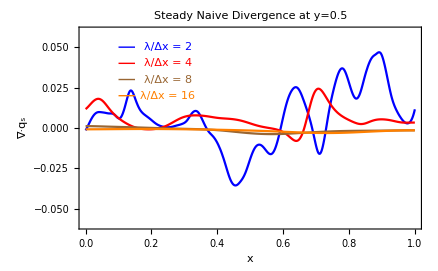

```mathematica
Plot[{divSteadyNaive[x,0.5,2],divSteadyNaive[x,0.5,4],divSteadyNaive[x,0.5,8],divSteadyNaive[x,0.5,16]},{x,0,1},PlotRange->{-0.06,0.06},
PlotLabel->"Steady Naive Divergence at y=0.5",PlotStyle->{Blue,Red,Brown,Orange},
Frame->True,FrameLabel->{"x","∇·q_s","",""},
Epilog->{Blue,Line[{{0.1,0.05},{0.15,0.05}}],Text["λ/Δx = 2",{0.25,0.05}],
Red,Line[{{0.1,0.04},{0.15,0.04}}],Text["λ/Δx = 4",{0.25,0.04}],
Brown,Line[{{0.1,0.03},{0.15,0.03}}],Text["λ/Δx = 8",{0.25,0.03}],
Orange,Line[{{0.1,0.02},{0.15,0.02}}],Text["λ/Δx = 16",{0.25,0.02}]}]
```

The plot shows that naive continuous solutions for small correlation lengths generate significant divergence errors, but these errors decline in magnitude as the correlation length increases.

### Self-consistency check

The procedures entailed in divergence-cleaning and enforcing the Continuity Equation lead to the modification of the solution dependent variables. Recall that the finite-difference solution provides the discrete heads h_ij(t) = h_(s; i,j)+h_(p; i,j) e^(ⅈ ω t) and discrete Darcy fluxes q_ij(t) = q_(s; i,j)+q_(p; i,j) e^(ⅈ ω t), and the discrete heads define the discrete porosities φ_ij(t) = φ_(s; i,j)+φ_(p; i,j) e^(ⅈ ω t) via the constitutive relation for compressibility. But discrete solutions are not fit for our purpose of examining coherent Lagrangian structures in the (continuous) flow domain. We need to move to continuous dependent variables.

A continuous interpolation is constructed for q^* that has a steady component with zero divergence everywhere, and a continuous interpolation is constructed for φ^* that satisfies the Continuity Equation jointly with q^*. The compressibility relation is then inverted to provide a continuous interpolation for h^*, resulting in 3 dependent variables (h^*, q^* and φ^*) that exactly satisfy the imposed physical constraints. However these three interpolations will not necessarily satisfy the original groundwater flow equation exactly - hopefully they will be "close" to a solution.

Another way to look at this process is to consider the inputs and outputs:
		FD solver						→			Physical constraints (div=0, CE, compressibility)
	input:  K_(i,j) and boundary conditions					input:  h_(i,j) , q_(i,j) and φ_(i,j)  (discrete)
	output:  h_(i,j) , q_(i,j) and φ_(i,j)							output:  h^* , q^* and φ^*  (interpolated)

Effective K

While the updated variables h^* , q^* and φ^* are mutually consistent with the applied physical constraints it is not clear whether they satisfy a groundwater flow equation. To determine this we invert the Darcy flux equation q^* = -K^* ∇h^* to estimate the effective conductivity value K^* implied by the updated variables. The uniqueness and statistics of the K^* estimates, and their relation to the K_(i,j) inputs, will throw light on the nature of the perturbations introduced in the physical constraint (updating) step.

Angular correlation

Another lens to examine the self-consistency through is by comparing the flux vector direction with the direction of the local head gradient. According to Darcy’s Law q = -K ∇h these two quantities are the inverse of each other. Writing q = (q_x,q_y), then the flux azimuth θ_q = ArcTan[q_x,q_y]. Similarly, if ∇h = (g_x,g_y) then the head gradient azimuth θ_(∇h) = ArcTan[g_x,g_y]. If the flux and head solutions are perfectly consistent, then plotting θ_q versus -θ_(∇h) should produce a 1:1 line.

#### Self-consistency of the steady finite difference solution

```mathematica
hsol = Partition[h,nx];
κEstimateFD[i_,j_]:= Module[{δ=L/(nx-1),κsamples,qlist,ghlist},
qlist = steadyFlux[[i,j]];
ghlist = {(hsol[[i+1,j]]-hsol[[i,j]]),(hsol[[i,j+1]]-hsol[[i,j]])}/δ;
κsamples = Chop[-qlist/ghlist];
Return[κsamples]
]
AzimuthEstimateFD[i_,j_]:= Module[{δ=L/(nx-1),azimuth,qlist,ghlist},
qlist = Chop[steadyFlux[[i,j]]];
ghlist = Chop[-κarray[[i,j]]{(hsol[[i+1,j]]-hsol[[i,j]]),(hsol[[i,j+1]]-hsol[[i,j]])}/δ];
azimuth = {ATanMGT[qlist],ATanMGT[ghlist]};
Return[Mod[azimuth,2π]-{π,π}]
]
κsampleFD = Flatten[Table[κEstimateFD[i,j],{i,2,nx-2},{j,2,ny-2}],1];
azsampleFD = Flatten[Table[AzimuthEstimateFD[i,j],{i,2,nx-2},{j,2,ny-2}],1];
KplotFD = Plot[x,{x,0,20},PlotRange->{{-2,20},{-2,20}},
PlotStyle->{{Black,Dashing[{0.02,0.02}]}},
PlotLabel->Style["K estimates from FD solution",{14,FontFamily->"Times",Black}],
AxesLabel->{"K_x/K_eff","K_y/K_eff"}, AxesStyle->Black,
Frame->False,AspectRatio->Automatic,
Epilog->{PointSize[0.005],Point/@(κsampleFD/κeff),Text["λ/Δ = "<>ToString[Round[ℓeff/Δx]],{5,15}],
Text["Unphysical values "<>ToString[NumberForm[100.*Total[1-UnitStep[κsampleFD /. {k1_,k2_}-> k1 k2]]/Length[κsampleFD],3]]<>"%",{14,3}]}];
azplotFD = Plot[x,{x,-π/2,π/2},PlotRange->{{-π/2-0.2,π/2+0.2},{-π/2-0.2,π/2+0.2}},
PlotStyle->{{Black,Dashing[{0.02,0.02}]}}, BaseStyle->{16,FontFamily->"Times",Black},
(*PlotLabel->Style["Azimuth correlation from FD solution",{14,FontFamily->"Times",Black}],*)
AxesLabel->{"θ_(q_(s;  m, n))","θ_(∇SubscriptBox[h, s;  m, n])"}, AxesStyle->Black,
Ticks->{{{-Pi/2,"-90°"},{-Pi/4,"-45°"},0,{Pi/4,"45°"},{Pi/2,"90°"}},{{-Pi/2,"-90°"},{-Pi/4,"-45°"},0,{Pi/4,"45°"},{Pi/2,"90°"}}},
Frame->False,AspectRatio->Automatic,
Epilog->{PointSize[0.005],Point/@(azsampleFD),Text[Style["λ/Δ = "<>ToString[Round[ℓeff/Δx]],{12,FontFamily->"Times"}],{-π/4,3.4π/8}],Text[Style["OverBar[Δθ] = "<>ToString[NumberForm[Mean[AffineNorm/@azsampleFD]/Degree,3]]<>"°",{12,FontFamily->"Times"}],{-π/4,3π/8}]}];
```

#### Self-consistency of the naive interpolation solution

```mathematica
hSteadyNaive=ListInterpolation[Partition[h//Chop,nx],{{0,L},{0,L}},InterpolationOrder->InterpOrder];ghNaive[x_,y_]=Grad[hSteadyNaive[x,y],{x,y}];
κEstimateNaive[x_,y_]:= Module[{ghlist,qlist,κsamples},
ghlist=ghNaive[x,y];
qlist={qxSteadyNaive[x,y],qySteadyNaive[x,y]};
κsamples = Chop[-qlist/ghlist];
Return[κsamples]
]
AzimuthEstimateNaive[x_,y_]:= Module[{azimuth,qlist,ghlist},
qlist = Chop[{qxSteadyNaive[x,y],qySteadyNaive[x,y]}];
ghlist = Chop[-ghNaive[x,y]];
azimuth = {ATanMGT[qlist],ATanMGT[ghlist]};
Return[Mod[azimuth,2π]-{π,π}]
]
δ = L/(nx-1);
κsampleNaive = Flatten[Table[κEstimateNaive[(i-1)*δ,(j-1)*δ],{i,2,nx-2},{j,2,ny-2}],1];
azsampleNaive = Flatten[Table[AzimuthEstimateNaive[(i-1)*δ,(j-1)*δ],{i,2,nx-2},{j,2,ny-2}],1];
KplotNaive = Plot[x,{x,0,20},PlotRange->{{-2,20},{-2,20}},
PlotStyle->{Dashing[{0.02,0.02}]},
PlotLabel->Style["K estimates from interpolation",{14,FontFamily->"Times",Black}],
AxesLabel->{"K_x/K_eff","K_y/K_eff"}, 
Frame->False,AspectRatio->Automatic,
Epilog->{PointSize[0.005],Point/@(κsampleNaive/κeff),Text["λ/Δ = "<>ToString[Round[ℓeff/Δx]],{5,15}],
Text["Unphysical values "<>ToString[NumberForm[100.*Total[1-UnitStep[κsampleNaive /. {k1_,k2_}-> k1 k2]]/Length[κsampleNaive],3]]<>"%",{14,3}]}];
azplotNaive = Plot[x,{x,-π/2,π/2},PlotRange->{{-π/2-0.2,π/2+0.2},{-π/2-0.2,π/2+0.2}},
PlotStyle->{{Black,Dashing[{0.02,0.02}]}}, BaseStyle->{16,FontFamily->"Times",Black},
(*PlotLabel->Style["Azimuth correlation from interpolation",{14,FontFamily->"Times",Black}],*)
AxesLabel->{"θ_(q_s^int)","θ_(∇SubsuperscriptBox[h, s, int])"}, AxesStyle->Black,
Ticks->{{{-Pi/2,"-90°"},{-Pi/4,"-45°"},0,{Pi/4,"45°"},{Pi/2,"90°"}},{{-Pi/2,"-90°"},{-Pi/4,"-45°"},0,{Pi/4,"45°"},{Pi/2,"90°"}}},
Frame->False,AspectRatio->Automatic,
Epilog->{PointSize[0.005],Point/@(azsampleNaive),Text[Style["λ/Δ = "<>ToString[Round[ℓeff/Δx]],{12,FontFamily->"Times"}],{-π/4,3.4π/8}],Text[Style["OverBar[Δθ] = "<>ToString[NumberForm[Mean[AffineNorm/@azsampleNaive]/Degree,3]]<>"°",{12,FontFamily->"Times"}],{-π/4,3π/8}]}];
```

#### Self-consistency of the solution constrained by CE correction

```mathematica
ghCE[x_,y_]=Grad[hCR[x,y],{x,y}];
κEstimateCE[x_,y_]:= Module[{ghlist,qlist,κsamples},
ghlist=ghCE[x,y]//Re;
qlist={qxSteady[x,y],qySteady[x,y]};
κsamples = Chop[-qlist/ghlist];
Return[κsamples]
]
AzimuthEstimateCE[x_,y_]:= Module[{azimuth,qlist,ghlist},
qlist = Chop[{qxSteady[x,y],qySteady[x,y]}];
ghlist = Chop[-ghCE[x,y]];
azimuth = {ATanMGT[qlist],ATanMGT[ghlist]};
Return[Mod[azimuth,2π]-{π,π}]
]
δ = L/(nx-1);
κsampleCE = Flatten[Table[κEstimateCE[(i-1)*δ,(j-1)*δ],{i,2,nx-2},{j,2,ny-2}],1];
azsampleCE = Flatten[Table[AzimuthEstimateCE[(i-1)*δ,(j-1)*δ],{i,2,nx-2},{j,2,ny-2}],1];
KplotCE = Plot[x,{x,0,20},PlotRange->{{-2,20},{-2,20}},
PlotStyle->{Dashing[{0.02,0.02}]},
PlotLabel->Style["K estimates from CE correction",{14,FontFamily->"Times",Black}],
AxesLabel->{"K_x/K_eff","K_y/K_eff"}, 
Frame->False,AspectRatio->Automatic,
Epilog->{PointSize[0.005],Point/@(κsampleCE/κeff),Text["λ/Δ = "<>ToString[Round[ℓeff/Δx]],{5,15}],
Text["Unphysical values "<>ToString[NumberForm[100.*Total[1-UnitStep[κsampleCE /. {k1_,k2_}-> k1 k2]]/Length[κsampleCE],3]]<>"%",{14,3}]}];
azplotCE = Plot[x,{x,-π/2,π/2},PlotRange->{{-π/2-0.2,π/2+0.2},{-π/2-0.2,π/2+0.2}},
PlotStyle->{{Black,Dashing[{0.02,0.02}]}}, BaseStyle->{16,FontFamily->"Times",Black},
(*PlotLabel->Style["Azimuth correlation from CE correction",{14,FontFamily->"Times",Black}],*)
AxesLabel->{"θ_(q_s^*)","θ_(∇SubsuperscriptBox[h, s, int])"}, AxesStyle->Black,
Ticks->{{{-Pi/2,"-90°"},{-Pi/4,"-45°"},0,{Pi/4,"45°"},{Pi/2,"90°"}},{{-Pi/2,"-90°"},{-Pi/4,"-45°"},0,{Pi/4,"45°"},{Pi/2,"90°"}}},
Frame->False,AspectRatio->Automatic,
Epilog->{PointSize[0.005],Point/@(azsampleCE),Text[Style["λ/Δ = "<>ToString[Round[ℓeff/Δx]],{12,FontFamily->"Times"}],{-π/4,3.4π/8}],Text[Style["OverBar[Δθ] = "<>ToString[NumberForm[Mean[AffineNorm/@azsampleCE]/Degree,3]]<>"°",{12,FontFamily->"Times"}],{-π/4,3π/8}]}];
```

#### Summary plots

Notes

1. 	All plots are samples compiled from FD grid node locations (no internodal samples). Therefore the sampling is consistent across all plots.

2.	Azimuths are calculated relative to the mean flow direction (i.e. right to left, or ±π) just because it gives a more appealing plot.

3. 	The FD solution has a very low error residual. Despite this there is significant scatter in the corresponding K and azimuth values, measured by the norm of 0.0552 (for ℓ_eff=2Δx). This is because the flux vectors are calculated at mid-nodal points where K is estimated by spatial averaging, whereas the head gradient is evaluated exactly on the grid node where K is known. Therefore the FD plots exhibit the fundamental difference between the head and flux solutions as constructed.

4.	Results are insensitive to (a) the choice of spatial conductivity averaging method, e.g. geometric or harmonic, and (b) the choice of Hermite or Spline interpolation of dependent variables. The latter is to be expected as both reproduce nodal values, but splines do provide continuous derivatives.

5.	Interpolation and CE correction generate significant dispersion in the correlation measures, including unphysical behaviour (negative K^⋆ and/or opposed azimuths). CE correction provides the worst self-consistency.

#### λ/Δx = 2

ℓ = 2 field from “C:/Users/4S/Dropbox/Tidal Mixing/fields/lnkl2v1.dat”

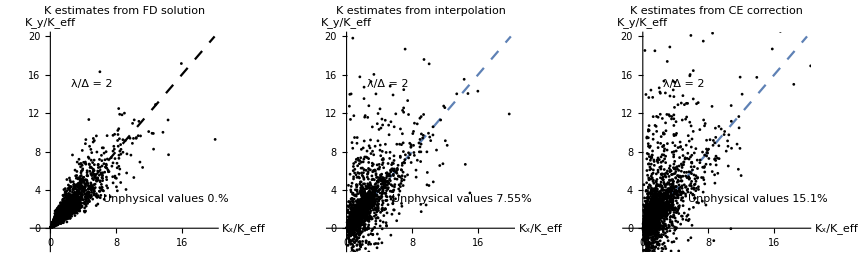

```mathematica
GraphicsGrid[{{KplotFD,KplotNaive,KplotCE}}]
```

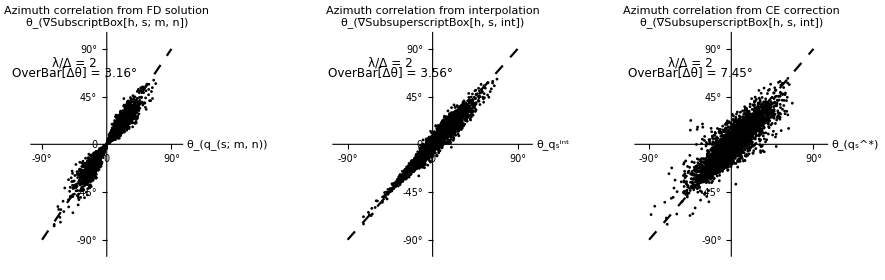

```mathematica
GraphicsGrid[{{azplotFD,azplotNaive,azplotCE}}]
```

#### λ/Δx = 4

ℓ = 4 field from “C:/Users/4S/Dropbox/Tidal Mixing/fields/FTLE_lnkl4v1dx1.dat”

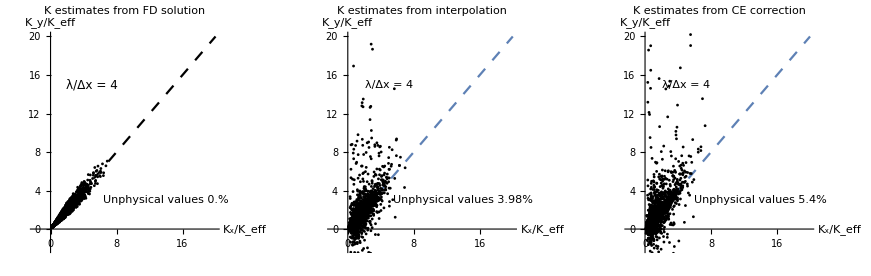

```mathematica
GraphicsGrid[{{KplotFD,KplotNaive,KplotCE}}]
```

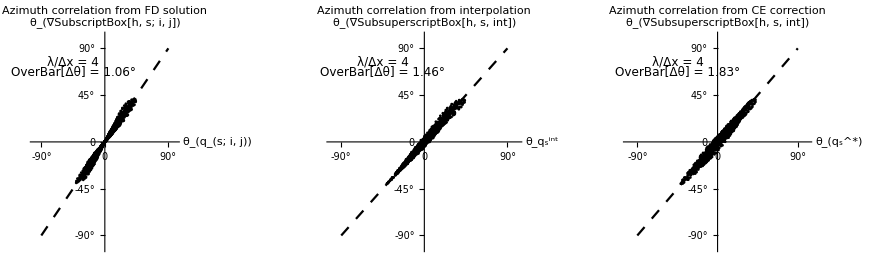

```mathematica
GraphicsGrid[{{azplotFD,azplotNaive,azplotCE}}]
```

#### λ/Δx = 6

ℓ = 6 field from “C:/Users/4S/Dropbox/Tidal Mixing/fields/FTLE_lnkl6v1dx1.dat”

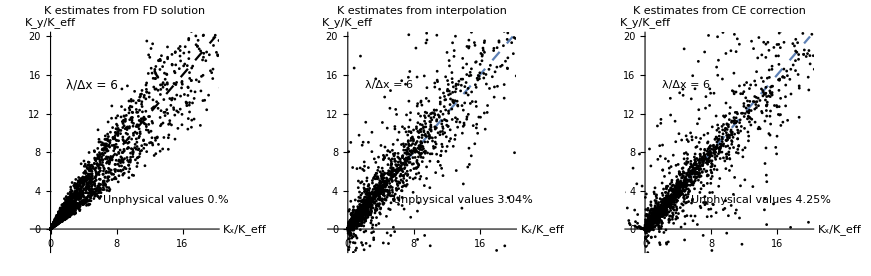

```mathematica
GraphicsGrid[{{KplotFD,KplotNaive,KplotCE}}]
```

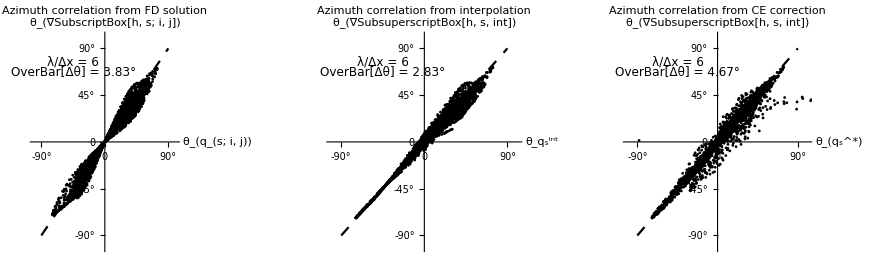

```mathematica
GraphicsGrid[{{azplotFD,azplotNaive,azplotCE}}]
```

#### λ/Δx = 8

ℓ = 8 field from “C:/Users/4S/Dropbox/Tidal Mixing/fields/FTLE_lnkl8v1dx1.dat”

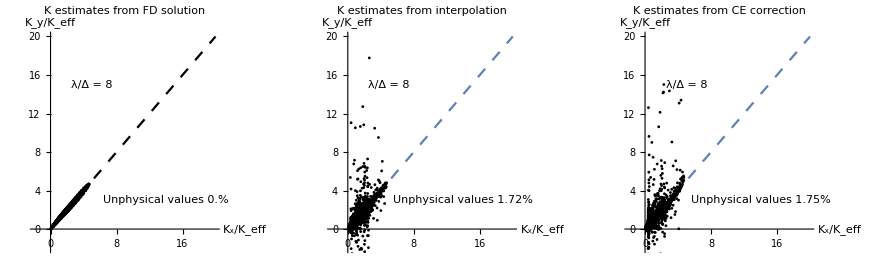

```mathematica
GraphicsGrid[{{KplotFD,KplotNaive,KplotCE}}]
```

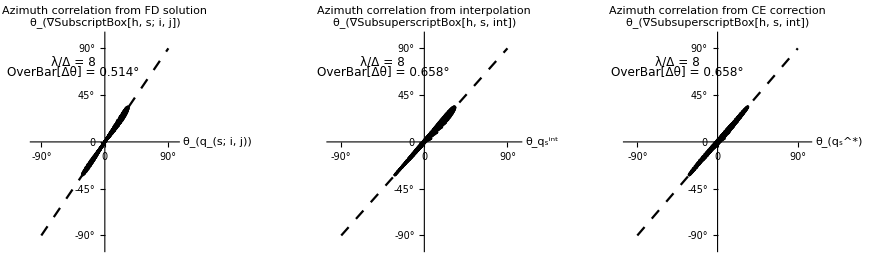

```mathematica
GraphicsGrid[{{azplotFD,azplotNaive,azplotCE}}]
```

#### λ/Δx = 10

ℓ = 10 field from “C:/Users/4S/Dropbox/Tidal Mixing/fields/lnkl10v1.dat”

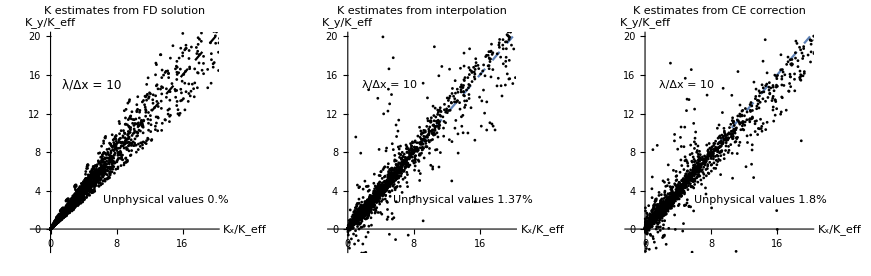

```mathematica
GraphicsGrid[{{KplotFD,KplotNaive,KplotCE}}]
```

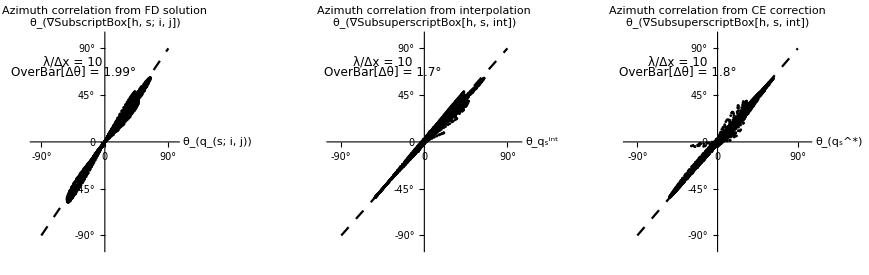

```mathematica
GraphicsGrid[{{azplotFD,azplotNaive,azplotCE}}]
```

#### λ/Δx = 12

ℓ = 12 field from “C:/Users/4S/Dropbox/Tidal Mixing/fields/lnkl12v1.dat”

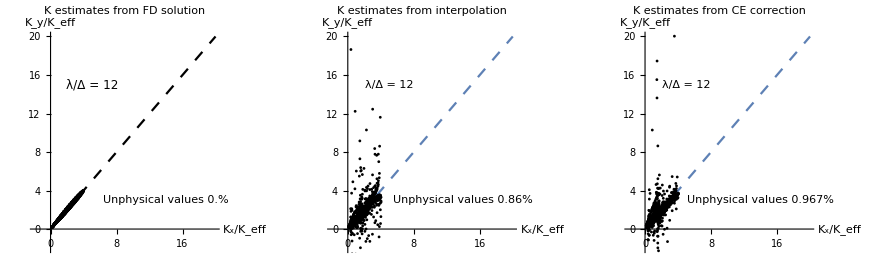

```mathematica
GraphicsGrid[{{KplotFD,KplotNaive,KplotCE}}]
```

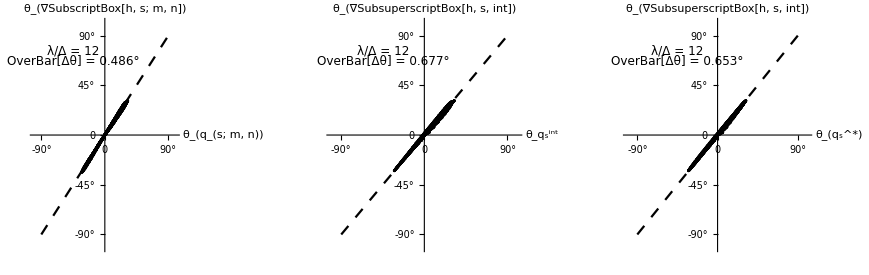

```mathematica
GraphicsGrid[{{azplotFD12,azplotNaive12,azplotCE12}}]
```

#### λ/Δx = 14

ℓ = 14 field from “C:/Users/4S/Dropbox/Tidal Mixing/fields/lnkl14v1.dat”

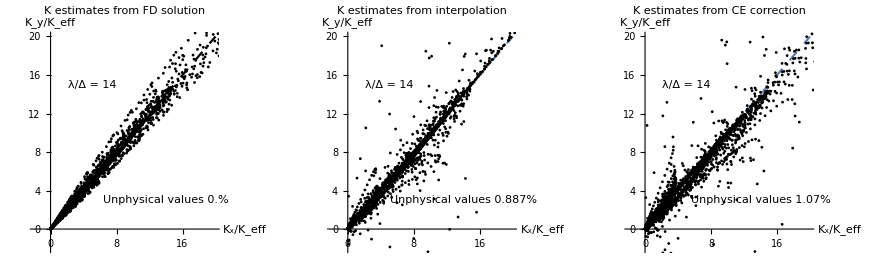

```mathematica
GraphicsGrid[{{KplotFD,KplotNaive,KplotCE}}]
```

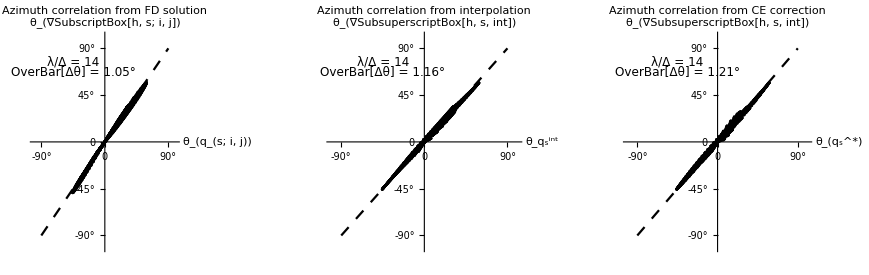

```mathematica
GraphicsGrid[{{azplotFD,azplotNaive,azplotCE}}]
```

#### λ/Δx = 16

ℓ = 16 field from “C:/Users/4S/Dropbox/Tidal Mixing/fields/FTLE_lnkl16v1dx1.dat”

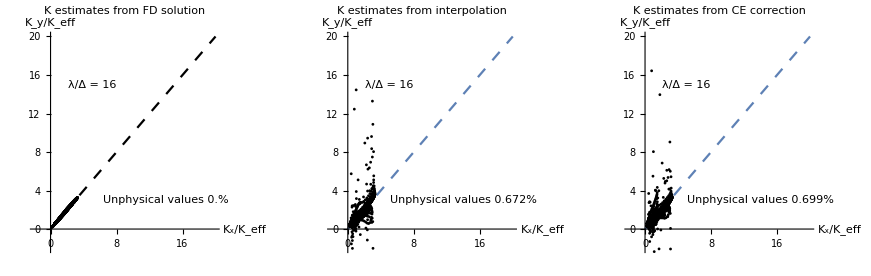

```mathematica
GraphicsGrid[{{KplotFD,KplotNaive,KplotCE}}]
```

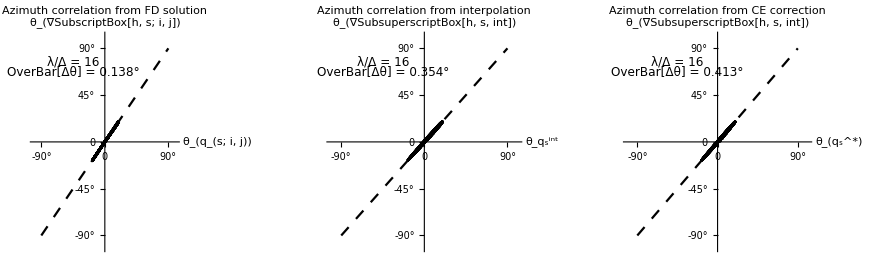

```mathematica
GraphicsGrid[{{azplotFD,azplotNaive,azplotCE}}]
```

#### Correlation length dependence of unphysical κ values and of mean azimuth error

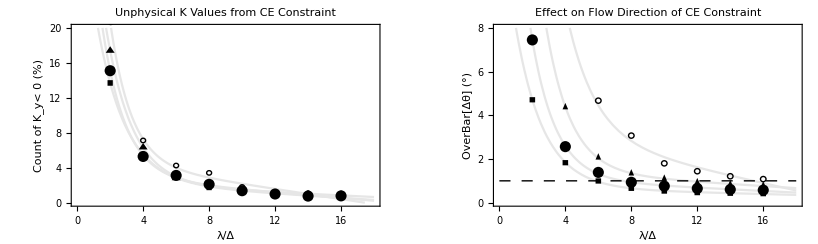

```mathematica
κunphysvsλp5 = {{2,13.7},{4,5.4}, {6,3.12},{8,1.75},{10,1.4},{12,0.967},{14,0.699},{16,0.699}};κunphysvsλ = {{2,15.1},{4,5.29}, {6,3.12},{8,2.1},{10,1.37},{12,0.994},{14,0.752},{16,0.779}};
κunphysvsλ2 = {{2,17.4},{4,6.34}, {6,2.82},{8,2.23},{10,1.42},{12,1.07},{14,0.967},{16,0.941}};
κunphysvsλ4 = {{2,20.7},{4,7.12}, {6,4.25},{8,3.41},{10,1.8},{12,0.806},{14,1.07},{16,0.833}};
empmodelunp = a Exp[-b x]+c + d x;
empfitunpp5 = FindFit[κunphysvsλp5,empmodelunp,{{a,10},{b,1},{c,0.05},{d,-0.01}},x];
empfitunp = FindFit[κunphysvsλ,empmodelunp,{{a,10},{b,1},{c,0.05},{d,-0.01}},x];
empfitunp2 = FindFit[κunphysvsλ2,empmodelunp,{{a,10},{b,1},{c,0.05},{d,-0.01}},x];
empfitunp4 = FindFit[κunphysvsλ4,empmodelunp,{{a,10},{b,1},{c,0.05},{d,-0.01}},x];
κunpPlot = Plot[{empmodelunp/.empfitunpp5,empmodelunp/.empfitunp,empmodelunp/.empfitunp2,empmodelunp/.empfitunp4},{x,1,18},PlotRange->{{0,18},{0,20}},
BaseStyle->{14,FontFamily->"Times",Black},PlotStyle->{GrayLevel[0.9]},PlotLabel->Style["Unphysical K Values from CE Constraint",{14,FontFamily->"Times",Black}],FrameStyle->Black,
FrameTicks->{{{0,4,8,12,16,20},{}},{{0,2,4,6,8,10,12,14,16,18},{}}},
Frame->True,FrameLabel->{"λ/Δ","Count of K_y< 0 (%)","",""},
Epilog->{(MGTRect[#,0.16{1,2}]&)/@κunphysvsλp5,PointSize[0.02],Point/@κunphysvsλ,(MGTTriangle[#,0.27{1,1.6}]&)/@κunphysvsλ2,(Circle[#,0.15{1,1.7}]&)/@κunphysvsλ4}];
azvsλp5 = {{2,4.71},{4,1.83},{6,0.993},{8,0.658},{10,0.532},{12,0.461},{14,0.431},{16,0.413}};
azvsλ = {{2,7.4497},{4,2.5652},{6,1.3867},{8,0.9347},{10,0.7595},{12,0.6532},{14,0.6039},{16,0.5744}};
azvsλ2 = {{2,13.1},{4,4.37},{6,2.07},{8,1.34},{10,1.1},{12,0.937},{14,0.845},{16,0.787}};
azvsλ4 = {{2,22.4},{4,8.74},{6,4.67},{8,3.07},{10,1.8},{12,1.44},{14,1.21},{16,1.08}};
empmodelaz = a Exp[-b x]+c + d x;
empfitazp5 = FindFit[azvsλp5,empmodelaz,{{a,10},{b,1},{c,0.05},{d,-0.01}},x];
empfitaz = FindFit[azvsλ,empmodelaz,{{a,10},{b,1},{c,0.05},{d,-0.01}},x];
empfitaz2 = FindFit[azvsλ2,empmodelaz,{{a,10},{b,1},{c,0.05},{d,-0.01}},x];
empfitaz4 = FindFit[azvsλ4,empmodelaz,{{a,20},{b,1},{c,0.05},{d,0}},x];
azPlot = Plot[{empmodelaz/.empfitazp5,empmodelaz/.empfitaz,empmodelaz/.empfitaz2,empmodelaz/.empfitaz4},{x,1,18},PlotRange->{{0,18},{0,8}},
BaseStyle->{14,FontFamily->"Times",Black},PlotStyle->{GrayLevel[0.9]},PlotLabel->Style["Effect on Flow Direction of CE Constraint",{14,FontFamily->"Times",Black}],FrameStyle->Black,
FrameTicks->{{{0,2,4,6,8},{}},{{0,2,4,6,8,10,12,14,16,18},{}}},
Frame->True,FrameLabel->{"λ/Δ","OverBar[Δθ] (°)","",""},
Epilog->{PointSize[0.02],(MGTRect[#,0.12{1.4,1}]&)/@azvsλp5,Point/@azvsλ,(MGTTriangle[#,0.17{1,1}]&)/@azvsλ2,(Circle[#,0.12{1.4,1}]&)/@azvsλ4,
Dashing[{0.02,0.02}],Line[{{0,1},{18,1}}]}];
summaryplot = GraphicsGrid[{{κunpPlot,azPlot}}]
```

```mathematica
Export["sc_summary.png",summaryplot,ImageSize->1200]
```

sc_summary.png

### Flux ellipses and eccentricities

```mathematica
Timing[CanonicalEllipseList = Table[{i,j,analyzeFluxEllipseByNode[i,j]},{i,2,nx-2},{j,3,ny-2}];]
CanonicalEllipseListFlat = Flatten[CanonicalEllipseList,1];
CanonicalEllipsePoints = DyadListToPoints[Table[{CanonicalEllipseListFlat[[i,1]],CanonicalEllipseListFlat[[i,2]],qualifyEllipse[CanonicalEllipseListFlat[[i,3]],"sense"]},{i,1,Length[CanonicalEllipseListFlat]}]];
CanonicalEccentricities = Table[Flatten[CanonicalEllipseList,1][[i,3,3]],{i,1,Length[Flatten[CanonicalEllipseList,1]]}];
CanonicalEccentricities = (Log[#]&) /@CanonicalEccentricities ;
```

{79.3281,Null}

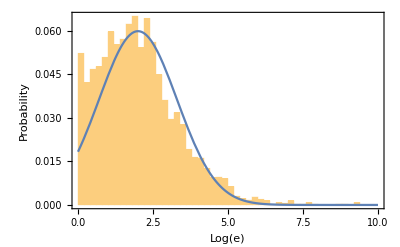

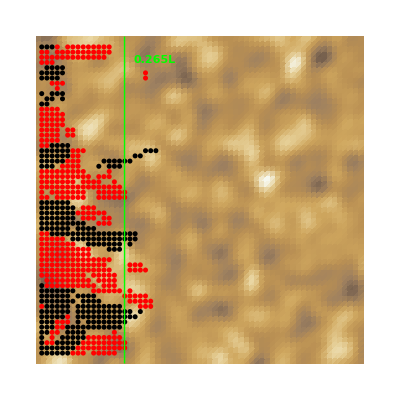

```mathematica
Show[Histogram[CanonicalEccentricities,70,"Probability",PlotRange->{{0,10},All},Frame->True,FrameLabel->{"Log(e)","Probability","",""}],Plot[0.195*PDF[NormalDistribution[2,1.3],x],{x,0,10}]]
xReversalZone = x/.FindRoot[Abs[uHyperbolicConstantDN[x,L,ω,κGeom,λ,τ,1,0]]-x*L,{x,0.2}];ListDensityPlot[Transpose[Log[κarray]],Frame->False,ColorFunction->"CoffeeTones",Epilog->{RGBColor[1,0,0],PointSize[0.009],CanonicalEllipsePoints,Green,Line[{{1+xReversalZone*nx,1},{1+xReversalZone*nx,1*ny}}],Text[Style[ToString[NumberForm[xReversalZone,3]]<>"L",Medium,Bold],{1+1.1*xReversalZone*nx,ny-0.07*ny},{-1,0}]}]
```

### Total porosity

```mathematica
Animate[Plot[{-1+Re[φTotal[x,0.25,t]]/φ0,-1+Re[φTotal[x,0.50,t]]/φ0,-1+Re[φTotal[x,0.75,t]]/φ0},{x,0,1},
PlotRange->{{0,1},{-0.02,0.02}},
PlotStyle->{Red,Blue,Brown},Epilog->{Text["t/P = "<>ToString[NumberForm[t/P,{10,3}]],{0.75,-0.015}]},
Epilog->{Red,Text["y = 0.25",{0.75,0.999}],Blue,Text["y = 0.50",{0.75,0.997}],Brown,Text["y = 0.75",{0.75,0.995}]},
Frame->True,FrameLabel->{"x","(φ-φ_0)/φ_0","",""},PlotLabel->"Porosity Variations, δ = u_0 S/φ_0",
FrameTicks->{{{{-3 S u0/φ0,"-3δ"},{-2 S u0/φ0,"-2δ"},{-S u0/φ0,"-δ"},{0,"0"},{S u0/φ0,"δ"},{0,"0"},{2 S u0/φ0,"2δ"},{3 S u0/φ0,"3δ"}},{{(hL-href)S/φ0,"h"}}},{{0,0.25,0.5,0.75,1},{Automatic}}},PlotLegends->{"y = 0.25","y = 0.50","y = 0.75"}],{t,0,P},AnimationRunning->False]
```

### Total flux components q_x and q_y

```mathematica
Animate[Row[{
Plot[{Re[qxInterp[x,0.25,t]],Re[qxInterp[x,0.50,t]],Re[qxInterp[x,0.75,t]]},{x,0,1},
PlotRange->{{0,1},{-0.005,0.005}},
PlotStyle->{Red,Blue,Brown},
ImageSize->300,
Epilog->{Text["t/P = "<>ToString[NumberForm[t/P,{10,3}]],{0.75,-0.003}],Red,Text["y = 0.25",{0.75,0.004}],Blue,Text["y = 0.50",{0.75,0.003}],Brown,Text["y = 0.75",{0.75,0.002}]},
Frame->True,FrameLabel->{"x","Total Longitudinal Flux q_x","",""},
FrameTicks->{{{-0.01,-0.005,0,0.005},{None}},{{0,0.25,0.5,0.75,1},{None}}}],
Plot[{Re[qyInterp[x,0.25,t]],Re[qyInterp[x,0.50,t]],Re[qyInterp[x,0.75,t]]},{x,0,1},
PlotRange->{{0,1},{-0.005,0.005}},
PlotStyle->{Red,Blue,Brown},
ImageSize->300,
Epilog->{Text["t/P = "<>ToString[NumberForm[t/P,{10,3}]],{0.75,-0.003}],Red,Text["y = 0.25",{0.75,0.004}],Blue,Text["y = 0.50",{0.75,0.003}],Brown,Text["y = 0.75",{0.75,0.002}]},
Frame->True,FrameLabel->{"x","Total Transverse Flux q_y","",""},
FrameTicks->{{{-0.005,0,0.005},{None}},{{0,0.25,0.5,0.75,1},{None}}}]}],
{t,0,P},ContentSize->700,AnimationRunning->False]
```

### Total velocity components v_x and v_y

```mathematica
Animate[Row[{
Plot[{Re[vxInterp[x,0.25,t,CASECOND]],Re[vxInterp[x,0.50,t,CASECOND]],Re[vxInterp[x,0.75,t,CASECOND]]},{x,0,1},
PlotRange->{{0,1},{-0.02,0.02}},
PlotStyle->{Red,Blue,Brown},
ImageSize->300,
Epilog->{Text["t/P = "<>ToString[NumberForm[t/P,{10,3}]],{0.75,-0.01}],Red,Text["y = 0.25",{0.75,0.015}],Blue,Text["y = 0.50",{0.75,0.01}],Brown,Text["y = 0.75",{0.75,0.005}]},
Frame->True,FrameLabel->{"x","Total Longitudinal Velocity v_x","",""},
FrameTicks->{{{-0.02,-0.01,0,0.01,0.02},{None}},{{0,0.25,0.5,0.75,1},{None}}}],
Plot[{Re[vyInterp[x,0.25,t,CASECOND]],Re[vyInterp[x,0.50,t,CASECOND]],Re[vyInterp[x,0.75,t,CASECOND]]},{x,0,1},
PlotRange->{{0,1},{-0.02,0.02}},
PlotStyle->{Red,Blue,Brown},
ImageSize->300,
Epilog->{Text["t/P = "<>ToString[NumberForm[t/P,{10,3}]],{0.75,-0.01}],Red,Text["y = 0.25",{0.75,0.015}],Blue,Text["y = 0.50",{0.75,0.01}],Brown,Text["y = 0.75",{0.75,0.005}]},
Frame->True,FrameLabel->{"x","Total Transverse Velocity v_y","",""},
FrameTicks->{{{-0.02,-0.01,0,0.01,0.02},{None}},{{0,0.25,0.5,0.75,1},{None}}}]}],
{t,0,P},ContentSize->700,AnimationRunning->False]
```

### Comparing velocities with fluxes

Let us compare v_x directly with q_x/φ_0 to gauge the magnitude of the correction arising from the compressible (elastic) porosity. Note that v ≡ q/φ and hence (v-q/φ_0)/v = 1-φ/φ_0, so the porosity-induced velocity correction is straightforward to calculate. But we will use the following formal expression:

```mathematica
δvx[x_,y_,t_,order_] := Re[(vxInterp[x,y,t,order]-qxInterp[x,y,t]/φ0)/vxInterp[x,y,t,order]]
```

```mathematica
Animate[
Row[{
Plot[{100*δvx[x,0.25,t,CAFIRST],100*δvx[x,0.5,t,CAFIRST],100*δvx[x,0.75,t,CAFIRST]},{x,0,1},
PlotStyle->{Red,Blue,Brown},
PlotRange->{-1,1},ImageSize->300,
Frame->True,FrameLabel->{"x","δv_x (%)","",""},
Epilog->{Text["φ = φ_s (1^st order)",{0.5,0.8}],Red,Text["y = 0.25",{0.8,0.5}],Blue,Text["y = 0.50",{0.8,0.3}],Brown,Text["y = 0.75",{0.8,0.1}]}],
Plot[{100*δvx[x,0.25,t,CASECOND],100*δvx[x,0.5,t,CASECOND],100*δvx[x,0.75,t,CASECOND]},{x,0,1},
PlotStyle->{Red,Blue,Brown},
PlotRange->{-1,1},ImageSize->300,
Frame->True,FrameLabel->{"x","δv_x (%)","",""},
Epilog->{Text["φ = φ_s+φ_p (2^nd order)",{0.5,0.8}],Red,Text["y = 0.25",{0.8,0.5}],Blue,Text["y = 0.50",{0.8,0.3}],Brown,Text["y = 0.75",{0.8,0.1}]}]
}],{t,0,P},ContentSize->700,AnimationRunning->False
]
```

The porosity-scaling discrepancy between the flux and the velocity is of the order of 1% or less.

### Flow paths

Let us consider how massless particles advect through the domain, starting from near the inland boundary and moving toward the tidal boundary.

```mathematica
tmax=10000P;
labelΔt = 100P;
x0 = 0.95; 

Timing[{tend1,{xend1,yend1}}=flowmap[x0,0.1,tmax,False]]
flowp1[t_]=flowpath[t];
times1 = Table[{Point[flowp1[i]],Text[ToString[i/labelΔt],flowp1[i]+{0,0.01}]},{i,0,tend1,labelΔt}];

Timing[{tend2,{xend2,yend2}}=flowmap[x0,0.2,tmax,False]]
flowp2[t_]=flowpath[t];
times2 = Table[{Point[flowp2[i]],Text[ToString[i/labelΔt],flowp2[i]+{0,0.01}]},{i,0,tend2,labelΔt}];

Timing[{tend3,{xtend3,ytend3}}=flowmap[x0,0.3,tmax,False]]
flowp3[t_]=flowpath[t];
times3= Table[{Point[flowp3[i]],Text[ToString[i/labelΔt],flowp3[i]+{0,0.01}]},{i,0,tend3,labelΔt}];

Timing[{tend4,{xtend4,ytend4}}=flowmap[x0,0.4,tmax,False]]
flowp4[t_]=flowpath[t];
times4= Table[{Point[flowp4[i]],Text[ToString[i/labelΔt],flowp4[i]+{0,0.01}]},{i,0,tend4,labelΔt}];

Timing[{tend5,{xtend5,ytend5}}=flowmap[x0,0.5,tmax,False]]
flowp5[t_]=flowpath[t];
times5= Table[{Point[flowp5[i]],Text[ToString[i/labelΔt],flowp5[i]+{0,0.01}]},{i,0,tend5,labelΔt}];

Timing[{tend6,{xtend6,ytend6}}=flowmap[x0,0.6,tmax,False]]
flowp6[t_]=flowpath[t];
times6 = Table[{Point[flowp6[i]],Text[ToString[i/labelΔt],flowp6[i]+{0,0.01}]},{i,0,tend6,labelΔt}];

Timing[{tend7,{xtend7,ytend7}}=flowmap[x0,0.7,tmax,False]]
flowp7[t_]=flowpath[t];
times7= Table[{Point[flowp7[i]],Text[ToString[i/labelΔt],flowp7[i]+{0,0.01}]},{i,0,tend7,labelΔt}];

Timing[{tend8,{xtend8,ytend8}}=flowmap[x0,0.8,tmax,False]]
flowp8[t_]=flowpath[t];
times8 = Table[{Point[flowp8[i]],Text[ToString[i/labelΔt],flowp8[i]+{0,0.01}]},{i,0,tend8,labelΔt}];

Timing[{tend9,{xtend9,ytend9}}=flowmap[x0,0.9,tmax,False]]
flowp9[t_]=flowpath[t];
times9 = Table[{Point[flowp9[i]],Text[ToString[i/labelΔt],flowp9[i]+{0,0.01}]},{i,0,tend9,labelΔt}];
```

clipping to boundary at time = 542.266 at location {-1.20699E-16,0.0755812}

{28.2344,{542.266,{-1.20699×10^-16,0.0755812}}}

clipping to boundary at time = 805.251 at location {-1.0272E-16,0.221348}

{28.75,{805.251,{-1.0272×10^-16,0.221348}}}

clipping to boundary at time = 660.763 at location {5.65378E-17,0.321561}

{26.8594,{660.763,{5.65378×10^-17,0.321561}}}

clipping to boundary at time = 813.276 at location {1.61546E-16,0.434125}

{33.5625,{813.276,{1.61546×10^-16,0.434125}}}

clipping to boundary at time = 390.746 at location {-1.2303E-16,0.561657}

{23.625,{390.746,{-1.2303×10^-16,0.561657}}}

clipping to boundary at time = 696.733 at location {-3.91594E-14,0.587892}

{28.5781,{696.733,{-3.91594×10^-14,0.587892}}}

clipping to boundary at time = 462.237 at location {-8.78598E-12,0.675292}

{24.6875,{462.237,{-8.78598×10^-12,0.675292}}}

clipping to boundary at time = 827.255 at location {-6.26669E-17,0.795798}

{28.6875,{827.255,{-6.26669×10^-17,0.795798}}}

clipping to boundary at time = 839.768 at location {2.45978E-17,0.873298}

{30.1406,{839.768,{2.45978×10^-17,0.873298}}}

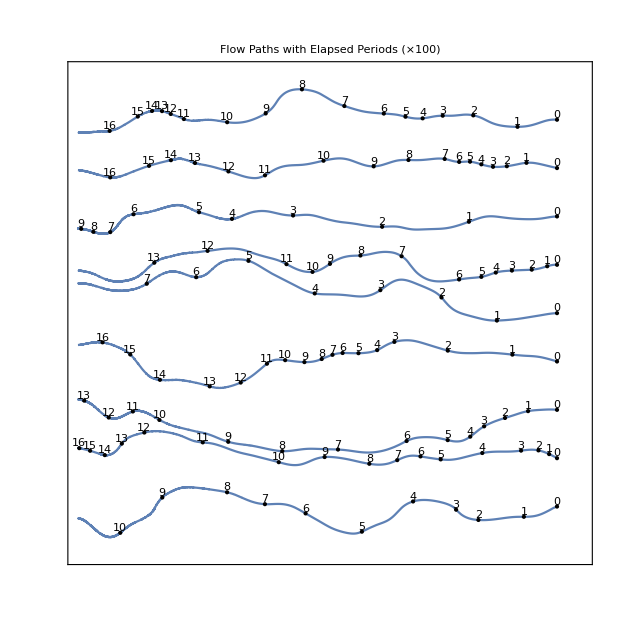

```mathematica
Show[ParametricPlot[flowp1[t],{t,0,tend1},PlotRange->{{0,1},{0,1}},Frame->True,FrameTicks->None,PlotLabel->"Flow Paths with Elapsed Periods (×"<>ToString[labelΔt/P]<>")",BaseStyle->{16,FontFamily->"Times"},Epilog->{times1,times2,times3,times4,times5,times6,times7,times8,times9}],
ParametricPlot[flowp2[t],{t,0,tend2},PlotRange->{{0,1},{0,1}},Frame->True,FrameTicks->None],
ParametricPlot[flowp3[t],{t,0,tend3},PlotRange->{{0,1},{0,1}},Frame->True,FrameTicks->None],
ParametricPlot[flowp4[t],{t,0,tend4},PlotRange->{{0,1},{0,1}},Frame->True,FrameTicks->None],
ParametricPlot[flowp5[t],{t,0,tend5},PlotRange->{{0,1},{0,1}},Frame->True,FrameTicks->None],
ParametricPlot[flowp6[t],{t,0,tend6},PlotRange->{{0,1},{0,1}},Frame->True,FrameTicks->None],
ParametricPlot[flowp7[t],{t,0,tend7},PlotRange->{{0,1},{0,1}},Frame->True,FrameTicks->None],
ParametricPlot[flowp8[t],{t,0,tend8},PlotRange->{{0,1},{0,1}},Frame->True,FrameTicks->None],
ParametricPlot[flowp9[t],{t,0,tend9},PlotRange->{{0,1},{0,1}},Frame->True,FrameTicks->None]]
```

The plot above shows the flow paths of the 9 particles as they meander through the heterogeneous domain. The digits show the number of elapsed tidal periods (×1000) along each path. The paths are not simple curves. The tidal fluctuations provide regular (in time) deflections of the paths, leading to many loops, as seen below in a zoomed view of part of flowpath7. The loop amplitudes depend on the problem parameters.

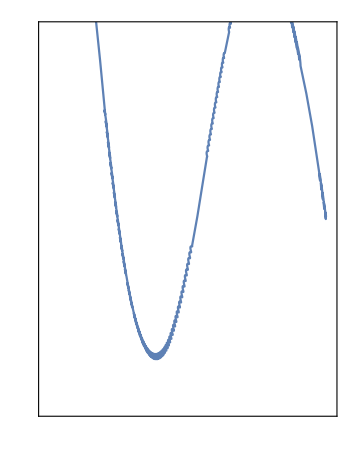

```mathematica
ParametricPlot[flowp3[t],{t,0.77tend3,0.955tend3},PlotRange->{{0.022,0.15},{0.28,0.295}},Frame->True,FrameTicks->None, AspectRatio->1.3]
```

### Poincaré sections

We calculate a Poincaré section with periodicity 𝒫 = 100 P, including 15000 points. This is a long calculation!

```mathematica
PSpts = {};
PSection[0.95,0.30,0,100P,15000,"zero",False]
```

Poincaré section formed and written to file PS_0.95_0.3_100_15000_zero.m in 12962.5 seconds.

```mathematica
ListDensityPlot[Log[κarray],PlotRange->All,DataRange->{{0,1},{0,1}},
Frame->False,PlotLabel->"Poincaré Section with 𝒫/P = 100",BaseStyle->{16,FontFamily->"Times"},
Epilog->{Black,PointSize[0.004],Point/@PSpts},ImageSize->450,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->150,LegendFunction->(Framed[#,RoundingRadius->5]&),LegendLabel->Style["Log κ",FontFamily->"Times",14]],{After,Center}],ColorFunction->"CoffeeTones"]
```

-Graphics-

### Residence time distributions

We need to calculate a well-sampled RTD along an arbitrary section in the domain.

{2852.44,Null}

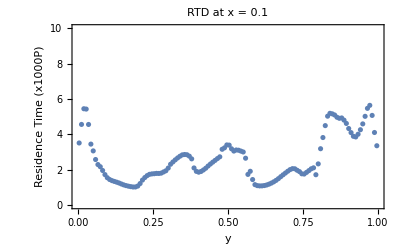

```mathematica
(rtd = ResidenceTimeDistribution[0.1,128];)// Timing
ListPlot[rtd/.{yy_,tt_}->{yy,tt/(1000P)},PlotRange->{{0,1},{0,10}},
Frame->True,FrameLabel->{"y","Residence Time (x1000P)","",""},BaseStyle->{16,FontFamily->"Times"},
PlotLabel->"RTD at x = 0.1"]
```

How does the RTD evolve with distance downstream?

{1439.33,Null}

{885.375,Null}

{484.922,Null}

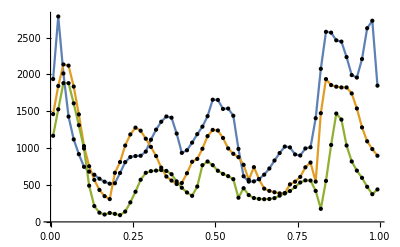

```mathematica
(rtdp1= ResidenceTimeDistribution[0.1,64];)// Timing
(rtdp4= ResidenceTimeDistribution[0.4,64];)// Timing
(rtdp7= ResidenceTimeDistribution[0.7,64];)// Timing
ListPlot[{rtdp1,rtdp4,rtdp7},Joined->True,PlotRange->All,Epilog->{Point/@rtdp1,Point/@rtdp4,Point/@rtdp7}]
```

### Lagrangian measures for Finite-Time Lyapunov Exponent (FTLE)

Here we calculate an arbitrary flow path

```mathematica
x0=0.99;y0=0.55;tmax = 1000;
Timing[{tend,{xtend,ytend}}=flowmapX[x0,y0,0,tmax,False]]
```

clipping to boundary at time = 844.221 at location {5.793E-13,0.503974}

{19.5625,{844.221,{5.7933×10^-13,0.503974}}}

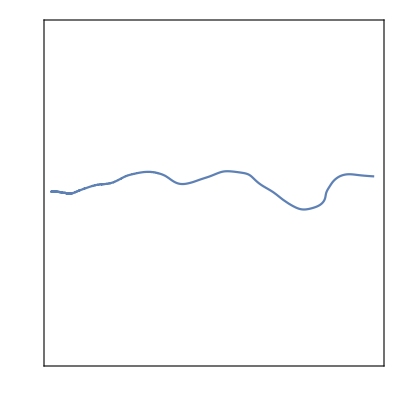

```mathematica
ParametricPlot[flowpath[t],{t,0,tend},PlotRange->{{0,1},{0,1}},Frame->True,FrameTicks->None]
```

Let us calculate the deformation tensor 𝔽 and the FTLE 𝕃  directly.

```mathematica
{xend,yend,tend}=LagrangeMeasuresExplicit[x0,y0,tmax];
```

clipping to boundary at time = 844.221 at location {5.793E-13,0.503974}

Preparing diagnostic plots ...

clipping to boundary at time = 844.221 at location {8.983E-12,0.503974}

clipping to boundary at time = 844.219 at location {-3.593E-13,0.503974}

```mathematica
diagplots =GraphicsGrid[{{Plot[𝔽[t],{t,0,tend},PlotRange->All,Frame->True,FrameLabel->{"t/P","𝔽 elements","",""},PlotStyle->{Thickness[0.002]},FrameStyle->Black],
LogPlot[{Abs[(Det[𝔽[t]]-φTotal[x0,y0,0]/φTotal[flowpath[t][[1]],flowpath[t][[2]],t])/Det[𝔽[t]]]},{t,0,tend},PlotRange->All,Frame->True,PlotPoints->400,PlotStyle->{Thickness[0.002]},FrameLabel->{"t/P","| (det 𝔽 - φ_0/φ) / det 𝔽 |","",""},FrameStyle->Black],
Plot[𝕃[t],{t,0,tend},PlotRange->{0,0.1},Frame->True,FrameLabel->{"t/P","𝕃","",""},PlotStyle->{Thickness[0.002]},FrameStyle->Black]
}}];
```

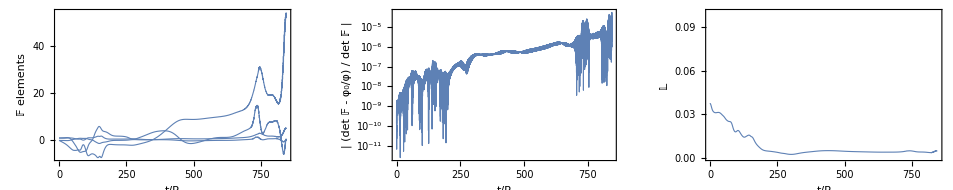

```mathematica
Show[diagplots]
```